## 6/11/19 Plot for A

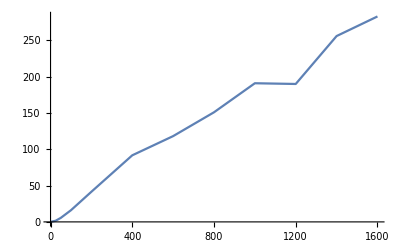

```mathematica
ListLinePlot[{{0,0},{25,1.5762534868431686},{50,5.505532770503416},{100,16.088472477593466},{200,41.53528980870369},{400,91.73090137346854},{600,118.17454494968081}, {800, 151}, {1000, 191}, {1200,190.},{1400,256.},{1600, 283}}]
```

## Plot for B

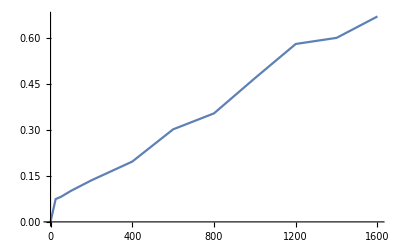

```mathematica
ListLinePlot[{{0,0},{25,0.07467020227864755},{50,0.08168672576381604},{100,0.101535},{200,0.1359759469052245},{400,0.19732939733914662},{600,0.3027684076573992},{800,0.355}, {1000,0.47}, {1200,0.582} , {1400, 0.602}, {1600,0.672}}]
```

## Plot for R

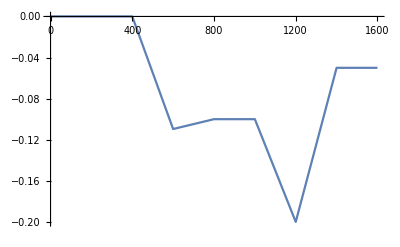

```mathematica
ListLinePlot[{{0,0},{25,0},{50,0},{100,0},{200,0},{400,0},{600,-0.10958188851836638},{800, -0.1}, {1000,-0.1}, {1200,-0.2} , {1400, -0.05}, {1600, -0.05}}]
```

## Refitted Data

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v25=blist[[3;;All,{14,3}]] 
FindFit[v25,a*(x/b)/(1+(x/b)^2),{a,b},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,0.114},{0.01,0.2},{0.015,0.311},{0.02,0.381},{0.025,0.457},{0.03,0.57},{0.035,0.668},{0.04,0.729},{0.045,0.768},{0.05,0.732},{0.055,0.707},{0.06,0.721},{0.065,0.672},{0.07,0.717},{0.075,0.749},{0.08,0.761},{0.085,0.766},{0.09,0.773},{0.095,0.756},{0.1,0.762},{0.105,0.763},{0.11,0.735},{0.115,0.73},{0.12,0.722},{0.125,0.713},{0.13,0.692},{0.135,0.682},{0.14,0.679},{0.145,0.677},{0.15,0.65},{0.155,0.641},{0.16,0.622},{0.165,0.587},{0.17,0.58},{0.175,0.584},{0.18,0.571},{0.185,0.559},{0.19,0.56},{0.195,0.543},{0.2,0.542},{0.205,0.521},{0.21,0.501},{0.215,0.504},{0.22,0.485},{0.225,0.476},{0.23,0.46},{0.235,0.462},{0.24,0.456},{0.245,0.452},{0.25,0.421},{0.255,0.427},{0.26,0.426},{0.265,0.421},{0.27,0.424},{0.275,0.414},{0.28,0.395},{0.285,0.397},{0.29,0.392},{0.295,0.381},{0.3,0.38},{0.305,0.359},{0.31,0.353},{0.315,0.357},{0.32,0.361},{0.325,0.359},{0.33,0.349},{0.335,0.342},{0.34,0.339},{0.345,0.318},{0.35,0.326},{0.355,0.322},{0.36,0.315},{0.365,0.32},{0.37,0.31},{0.375,0.301},{0.38,0.3},{0.385,0.304},{0.39,0.298},{0.395,0.291},{0.4,0.288},{0.405,0.287},{0.41,0.278},{0.415,0.282},{0.42,0.274},{0.425,0.27},{0.43,0.27},{0.435,0.269},{0.44,0.268},{0.445,0.262},{0.45,0.253},{0.455,0.247},{0.46,0.25},{0.465,0.244},{0.47,0.249},{0.475,0.245},{0.48,0.24},{0.485,0.239},{0.49,0.238},{0.495,0.231},{0.5,0.232},{0.505,0.235},{0.51,0.23},{0.515,0.221},{0.52,0.213},{0.525,0.22},{0.53,0.208},{0.535,0.217},{0.54,0.215},{0.545,0.214},{0.55,0.209},{0.555,0.204},{0.56,0.204},{0.565,0.207},{0.57,0.202},{0.575,0.198},{0.58,0.197},{0.585,0.198},{0.59,0.194},{0.595,0.19},{0.6,0.191},{0.605,0.193},{0.61,0.187},{0.615,0.189},{0.62,0.183},{0.625,0.184},{0.63,0.186},{0.635,0.178},{0.64,0.179},{0.645,0.178},{0.65,0.177},{0.655,0.175},{0.66,0.175},{0.665,0.171},{0.67,0.172},{0.675,0.168},{0.68,0.164},{0.685,0.165},{0.69,0.167},{0.695,0.164},{0.7,0.165},{0.705,0.164},{0.71,0.156},{0.715,0.154},{0.72,0.158},{0.725,0.156},{0.73,0.155},{0.735,0.157},{0.74,0.156},{0.745,0.152},{0.75,0.154},{0.755,0.15},{0.76,0.148},{0.765,0.148},{0.77,0.149},{0.775,0.144},{0.78,0.145},{0.785,0.147},{0.79,0.145},{0.795,0.137},{0.8,0.141},{0.805,0.141},{0.81,0.14},{0.815,0.139},{0.82,0.139},{0.825,0.14},{0.83,0.135},{0.835,0.138},{0.84,0.138},{0.845,0.136},{0.85,0.134},{0.855,0.132},{0.86,0.131},{0.865,0.133},{0.87,0.13},{0.875,0.132},{0.88,0.129},{0.885,0.13},{0.89,0.121},{0.895,0.124},{0.9,0.125},{0.905,0.125},{0.91,0.125},{0.915,0.126},{0.92,0.126},{0.925,0.125},{0.93,0.123},{0.935,0.122},{0.94,0.123},{0.945,0.12},{0.95,0.12},{0.955,0.117},{0.96,0.12},{0.965,0.12},{0.97,0.119},{0.975,0.117},{0.98,0.116},{0.985,0.112},{0.99,0.116},{0.995,0.114},{1,0.113},{1.005,0.109},{1.01,0.11},{1.015,0.111},{1.02,0.111},{1.025,0.11},{1.03,0.109},{1.035,0.108},{1.04,0.105},{1.045,0.108},{1.05,0.106},{1.055,0.105},{1.06,0.105},{1.065,0.104},{1.07,0.104},{1.075,0.102},{1.08,0.103},{1.085,0.102},{1.09,0.103},{1.095,0.102},{1.1,0.097},{1.105,0.097},{1.11,0.097},{1.115,0.097},{1.12,0.095},{1.125,0.098},{1.13,0.099},{1.135,0.099},{1.14,0.097},{1.145,0.096},{1.15,0.095},{1.155,0.097},{1.16,0.097},{1.165,0.093},{1.17,0.095},{1.175,0.094},{1.18,0.094},{1.185,0.094},{1.19,0.093},{1.195,0.093},{1.2,0.091},{1.205,0.09},{1.21,0.091},{1.215,0.09},{1.22,0.091},{1.225,0.091},{1.23,0.089},{1.235,0.086},{1.24,0.089},{1.245,0.089},{1.25,0.084},{1.255,0.086},{1.26,0.088},{1.265,0.085},{1.27,0.086},{1.275,0.086},{1.28,0.084},{1.285,0.082},{1.29,0.085},{1.295,0.085},{1.3,0.083},{1.305,0.082},{1.31,0.082},{1.315,0.084},{1.32,0.081},{1.325,0.082},{1.33,0.082},{1.335,0.082},{1.34,0.079},{1.345,0.079},{1.35,0.08},{1.355,0.081},{1.36,0.077},{1.365,0.08},{1.37,0.08},{1.375,0.08},{1.38,0.079},{1.385,0.078},{1.39,0.079},{1.395,0.079},{1.4,0.078},{1.405,0.076},{1.41,0.076},{1.415,0.075},{1.42,0.075},{1.425,0.075},{1.43,0.073},{1.435,0.074},{1.44,0.075},{1.445,0.074},{1.45,0.074},{1.455,0.073},{1.46,0.073},{1.465,0.073},{1.47,0.074},{1.475,0.073},{1.48,0.072},{1.485,0.073},{1.49,0.072},{1.495,0.071},{1.5,0.071},{1.505,0.071},{1.51,0.071},{1.515,0.071},{1.52,0.071},{1.525,0.067},{1.53,0.069},{1.535,0.067},{1.54,0.066},{1.545,0.069},{1.55,0.069},{1.555,0.067},{1.56,0.065},{1.565,0.066},{1.57,0.065},{1.575,0.065},{1.58,0.065},{1.585,0.067},{1.59,0.066},{1.595,0.065},{1.6,0.066},{1.605,0.063},{1.61,0.064},{1.615,0.064},{1.62,0.064},{1.625,0.062},{1.63,0.062},{1.635,0.062},{1.64,0.064},{1.645,0.062},{1.65,0.064},{1.655,0.064},{1.66,0.064},{1.665,0.062},{1.67,0.064},{1.675,0.063},{1.68,0.062},{1.685,0.063},{1.69,0.062},{1.695,0.062},{1.7,0.062},{1.705,0.062},{1.71,0.06},{1.715,0.062},{1.72,0.06},{1.725,0.061},{1.73,0.059},{1.735,0.059},{1.74,0.06},{1.745,0.06},{1.75,0.059},{1.755,0.059},{1.76,0.059},{1.765,0.059},{1.77,0.059},{1.775,0.058},{1.78,0.058},{1.785,0.058},{1.79,0.059},{1.795,0.058},{1.8,0.057},{1.805,0.056},{1.81,0.057},{1.815,0.057},{1.82,0.053},{1.825,0.057},{1.83,0.057},{1.835,0.056},{1.84,0.054},{1.845,0.055},{1.85,0.056},{1.855,0.056},{1.86,0.054},{1.865,0.056},{1.87,0.052},{1.875,0.054},{1.88,0.054},{1.885,0.054},{1.89,0.054},{1.895,0.054},{1.9,0.054},{1.905,0.053},{1.91,0.052},{1.915,0.054},{1.92,0.052},{1.925,0.052},{1.93,0.053},{1.935,0.054},{1.94,0.052},{1.945,0.052},{1.95,0.053},{1.955,0.052},{1.96,0.053},{1.965,0.053},{1.97,0.051},{1.975,0.052},{1.98,0.05},{1.985,0.05},{1.99,0.05},{1.995,0.049},{2,0.05}}

{a→1.57625,b→0.0746702}

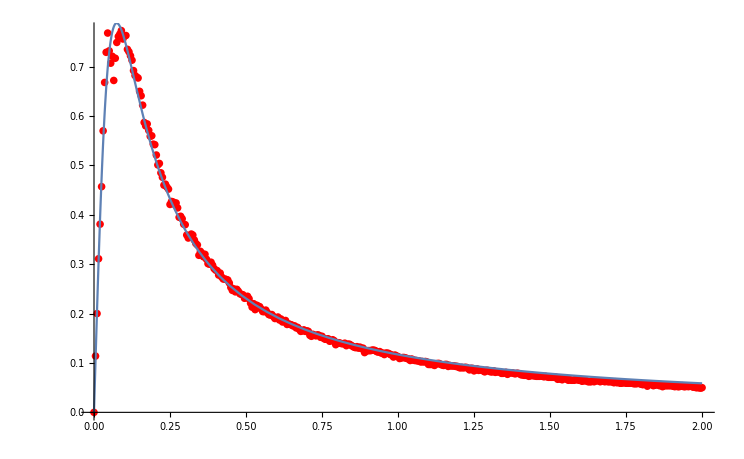

```mathematica
Show[ListPlot[v25,PlotStyle->Red],Plot[(a x)/(b (1+(x/b)^2))/.{a->1.5762534868431686,b->0.07467020227864755},{x,0,2}]]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v50=blist[[3;;All,{14,4}]] 
FindFit[v50,a*(x/b)/(1+(x/b)^2),{a,b},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,0.43},{0.01,0.623},{0.015,0.946},{0.02,1.293},{0.025,1.515},{0.03,1.776},{0.035,1.995},{0.04,2.176},{0.045,2.396},{0.05,2.505},{0.055,2.567},{0.06,2.657},{0.065,2.716},{0.07,2.758},{0.075,2.702},{0.08,2.692},{0.085,2.748},{0.09,2.72},{0.095,2.666},{0.1,2.657},{0.105,2.606},{0.11,2.606},{0.115,2.568},{0.12,2.572},{0.125,2.447},{0.13,2.431},{0.135,2.426},{0.14,2.38},{0.145,2.351},{0.15,2.331},{0.155,2.285},{0.16,2.235},{0.165,2.201},{0.17,2.161},{0.175,2.098},{0.18,2.07},{0.185,2.008},{0.19,1.99},{0.195,1.985},{0.2,1.892},{0.205,1.901},{0.21,1.878},{0.215,1.846},{0.22,1.832},{0.225,1.787},{0.23,1.771},{0.235,1.73},{0.24,1.702},{0.245,1.676},{0.25,1.662},{0.255,1.64},{0.26,1.62},{0.265,1.58},{0.27,1.56},{0.275,1.518},{0.28,1.511},{0.285,1.472},{0.29,1.465},{0.295,1.393},{0.3,1.411},{0.305,1.386},{0.31,1.382},{0.315,1.363},{0.32,1.358},{0.325,1.316},{0.33,1.307},{0.335,1.297},{0.34,1.283},{0.345,1.238},{0.35,1.21},{0.355,1.235},{0.36,1.222},{0.365,1.186},{0.37,1.185},{0.375,1.142},{0.38,1.156},{0.385,1.141},{0.39,1.132},{0.395,1.083},{0.4,1.116},{0.405,1.098},{0.41,1.082},{0.415,1.05},{0.42,1.048},{0.425,1.036},{0.43,1.02},{0.435,1.04},{0.44,1.026},{0.445,1.005},{0.45,0.992},{0.455,0.98},{0.46,0.971},{0.465,0.953},{0.47,0.958},{0.475,0.927},{0.48,0.94},{0.485,0.92},{0.49,0.895},{0.495,0.913},{0.5,0.862},{0.505,0.891},{0.51,0.836},{0.515,0.862},{0.52,0.853},{0.525,0.851},{0.53,0.843},{0.535,0.833},{0.54,0.833},{0.545,0.832},{0.55,0.788},{0.555,0.817},{0.56,0.812},{0.565,0.802},{0.57,0.798},{0.575,0.776},{0.58,0.785},{0.585,0.761},{0.59,0.76},{0.595,0.757},{0.6,0.722},{0.605,0.738},{0.61,0.74},{0.615,0.727},{0.62,0.711},{0.625,0.711},{0.63,0.721},{0.635,0.691},{0.64,0.67},{0.645,0.685},{0.65,0.66},{0.655,0.671},{0.66,0.666},{0.665,0.663},{0.67,0.656},{0.675,0.643},{0.68,0.643},{0.685,0.651},{0.69,0.626},{0.695,0.638},{0.7,0.642},{0.705,0.632},{0.71,0.627},{0.715,0.603},{0.72,0.621},{0.725,0.581},{0.73,0.605},{0.735,0.6},{0.74,0.61},{0.745,0.6},{0.75,0.6},{0.755,0.59},{0.76,0.596},{0.765,0.58},{0.77,0.572},{0.775,0.565},{0.78,0.558},{0.785,0.571},{0.79,0.575},{0.795,0.562},{0.8,0.557},{0.805,0.55},{0.81,0.545},{0.815,0.542},{0.82,0.536},{0.825,0.526},{0.83,0.533},{0.835,0.53},{0.84,0.523},{0.845,0.531},{0.85,0.511},{0.855,0.512},{0.86,0.516},{0.865,0.515},{0.87,0.51},{0.875,0.516},{0.88,0.513},{0.885,0.505},{0.89,0.498},{0.895,0.495},{0.9,0.49},{0.905,0.496},{0.91,0.486},{0.915,0.486},{0.92,0.482},{0.925,0.471},{0.93,0.472},{0.935,0.476},{0.94,0.478},{0.945,0.467},{0.95,0.47},{0.955,0.465},{0.96,0.465},{0.965,0.443},{0.97,0.465},{0.975,0.455},{0.98,0.46},{0.985,0.455},{0.99,0.437},{0.995,0.445},{1,0.442},{1.005,0.44},{1.01,0.437},{1.015,0.437},{1.02,0.43},{1.025,0.427},{1.03,0.431},{1.035,0.423},{1.04,0.418},{1.045,0.425},{1.05,0.417},{1.055,0.4},{1.06,0.411},{1.065,0.408},{1.07,0.408},{1.075,0.412},{1.08,0.413},{1.085,0.406},{1.09,0.406},{1.095,0.407},{1.1,0.392},{1.105,0.385},{1.11,0.388},{1.115,0.386},{1.12,0.386},{1.125,0.376},{1.13,0.383},{1.135,0.377},{1.14,0.383},{1.145,0.363},{1.15,0.375},{1.155,0.378},{1.16,0.378},{1.165,0.377},{1.17,0.372},{1.175,0.375},{1.18,0.372},{1.185,0.366},{1.19,0.368},{1.195,0.361},{1.2,0.361},{1.205,0.365},{1.21,0.365},{1.215,0.363},{1.22,0.356},{1.225,0.341},{1.23,0.351},{1.235,0.337},{1.24,0.346},{1.245,0.351},{1.25,0.338},{1.255,0.347},{1.26,0.337},{1.265,0.333},{1.27,0.34},{1.275,0.343},{1.28,0.333},{1.285,0.337},{1.29,0.332},{1.295,0.338},{1.3,0.331},{1.305,0.332},{1.31,0.327},{1.315,0.331},{1.32,0.32},{1.325,0.323},{1.33,0.322},{1.335,0.318},{1.34,0.322},{1.345,0.316},{1.35,0.32},{1.355,0.32},{1.36,0.318},{1.365,0.312},{1.37,0.317},{1.375,0.312},{1.38,0.31},{1.385,0.311},{1.39,0.303},{1.395,0.301},{1.4,0.295},{1.405,0.306},{1.41,0.305},{1.415,0.301},{1.42,0.287},{1.425,0.3},{1.43,0.297},{1.435,0.296},{1.44,0.296},{1.445,0.297},{1.45,0.297},{1.455,0.296},{1.46,0.297},{1.465,0.287},{1.47,0.276},{1.475,0.29},{1.48,0.288},{1.485,0.286},{1.49,0.28},{1.495,0.283},{1.5,0.276},{1.505,0.283},{1.51,0.282},{1.515,0.272},{1.52,0.276},{1.525,0.28},{1.53,0.272},{1.535,0.271},{1.54,0.273},{1.545,0.272},{1.55,0.261},{1.555,0.266},{1.56,0.247},{1.565,0.265},{1.57,0.263},{1.575,0.262},{1.58,0.267},{1.585,0.268},{1.59,0.262},{1.595,0.266},{1.6,0.266},{1.605,0.258},{1.61,0.253},{1.615,0.255},{1.62,0.257},{1.625,0.258},{1.63,0.253},{1.635,0.252},{1.64,0.253},{1.645,0.257},{1.65,0.252},{1.655,0.252},{1.66,0.243},{1.665,0.252},{1.67,0.248},{1.675,0.248},{1.68,0.247},{1.685,0.245},{1.69,0.24},{1.695,0.246},{1.7,0.247},{1.705,0.243},{1.71,0.236},{1.715,0.237},{1.72,0.242},{1.725,0.238},{1.73,0.24},{1.735,0.241},{1.74,0.238},{1.745,0.237},{1.75,0.235},{1.755,0.231},{1.76,0.226},{1.765,0.231},{1.77,0.231},{1.775,0.232},{1.78,0.228},{1.785,0.233},{1.79,0.231},{1.795,0.227},{1.8,0.227},{1.805,0.227},{1.81,0.228},{1.815,0.227},{1.82,0.222},{1.825,0.225},{1.83,0.225},{1.835,0.222},{1.84,0.223},{1.845,0.213},{1.85,0.223},{1.855,0.22},{1.86,0.218},{1.865,0.216},{1.87,0.21},{1.875,0.211},{1.88,0.213},{1.885,0.216},{1.89,0.217},{1.895,0.215},{1.9,0.215},{1.905,0.215},{1.91,0.215},{1.915,0.215},{1.92,0.212},{1.925,0.212},{1.93,0.208},{1.935,0.205},{1.94,0.207},{1.945,0.211},{1.95,0.207},{1.955,0.201},{1.96,0.208},{1.965,0.202},{1.97,0.205},{1.975,0.193},{1.98,0.202},{1.985,0.206},{1.99,0.198},{1.995,0.195},{2,0.202}}

{a→5.50553,b→0.0816867}

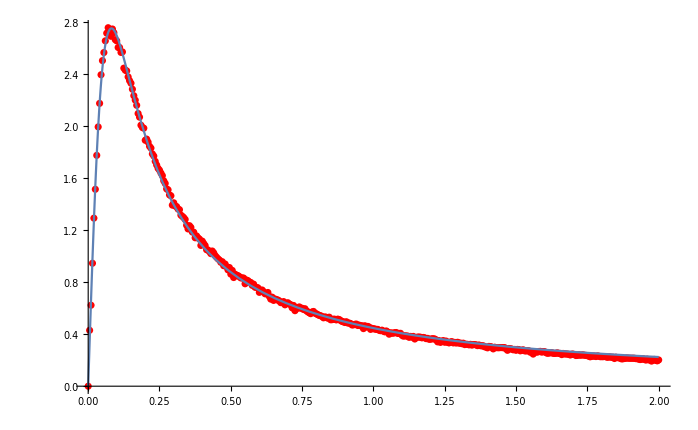

```mathematica
Show[ListPlot[v50,PlotStyle->Red],Plot[(a x)/(b (1+(x/b)^2))/.{a->5.505532770503416,b->0.08168672576381604},{x,0,2}]]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v100=blist[[3;;All,{14,5}]] 
FindFit[v100,a*(x/b)/(1+(x/b)^2),{a,b},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,1.135},{0.01,1.63},{0.015,2.28},{0.02,3.115},{0.025,3.9},{0.03,4.545},{0.035,5.235},{0.04,5.805},{0.045,6.165},{0.05,6.53},{0.055,6.885},{0.06,7.355},{0.065,7.355},{0.07,7.57},{0.075,7.66},{0.08,7.845},{0.085,7.925},{0.09,7.975},{0.095,7.87},{0.1,7.87},{0.105,7.87},{0.11,8.02},{0.115,7.88},{0.12,7.74},{0.125,7.57},{0.13,7.68},{0.135,7.615},{0.14,7.44},{0.145,7.365},{0.15,7.145},{0.155,7.165},{0.16,7.03},{0.165,6.985},{0.17,7.08},{0.175,6.86},{0.18,6.77},{0.185,6.425},{0.19,6.38},{0.195,6.48},{0.2,6.46},{0.205,6.345},{0.21,6.22},{0.215,6.145},{0.22,6.07},{0.225,6.04},{0.23,5.845},{0.235,5.865},{0.24,5.735},{0.245,5.625},{0.25,5.57},{0.255,5.355},{0.26,5.295},{0.265,5.425},{0.27,5.17},{0.275,5.28},{0.28,5.21},{0.285,5.08},{0.29,4.945},{0.295,4.94},{0.3,4.94},{0.305,4.925},{0.31,4.835},{0.315,4.795},{0.32,4.7},{0.325,4.705},{0.33,4.55},{0.335,4.6},{0.34,4.42},{0.345,4.5},{0.35,4.26},{0.355,4.34},{0.36,4.225},{0.365,4.265},{0.37,4.23},{0.375,4.205},{0.38,4.065},{0.385,4.065},{0.39,4.055},{0.395,3.84},{0.4,3.945},{0.405,3.825},{0.41,3.805},{0.415,3.785},{0.42,3.815},{0.425,3.725},{0.43,3.68},{0.435,3.69},{0.44,3.62},{0.445,3.56},{0.45,3.385},{0.455,3.52},{0.46,3.51},{0.465,3.45},{0.47,3.395},{0.475,3.42},{0.48,3.33},{0.485,3.35},{0.49,3.34},{0.495,3.265},{0.5,3.175},{0.505,3.165},{0.51,3.13},{0.515,3.105},{0.52,3.14},{0.525,3.07},{0.53,2.99},{0.535,3.075},{0.54,3.03},{0.545,2.955},{0.55,2.935},{0.555,2.895},{0.56,2.8},{0.565,2.835},{0.57,2.79},{0.575,2.83},{0.58,2.825},{0.585,2.715},{0.59,2.78},{0.595,2.74},{0.6,2.62},{0.605,2.665},{0.61,2.665},{0.615,2.655},{0.62,2.635},{0.625,2.655},{0.63,2.59},{0.635,2.565},{0.64,2.555},{0.645,2.485},{0.65,2.555},{0.655,2.51},{0.66,2.425},{0.665,2.42},{0.67,2.465},{0.675,2.44},{0.68,2.435},{0.685,2.425},{0.69,2.38},{0.695,2.4},{0.7,2.345},{0.705,2.36},{0.71,2.32},{0.715,2.23},{0.72,2.275},{0.725,2.285},{0.73,2.29},{0.735,2.27},{0.74,2.23},{0.745,2.15},{0.75,2.125},{0.755,2.205},{0.76,2.14},{0.765,2.17},{0.77,2.17},{0.775,2.09},{0.78,2.095},{0.785,2.095},{0.79,2.075},{0.795,2.095},{0.8,2.065},{0.805,2.05},{0.81,2.02},{0.815,2.035},{0.82,2.02},{0.825,1.995},{0.83,1.98},{0.835,1.975},{0.84,1.995},{0.845,1.97},{0.85,1.945},{0.855,1.925},{0.86,1.945},{0.865,1.94},{0.87,1.905},{0.875,1.885},{0.88,1.89},{0.885,1.88},{0.89,1.87},{0.895,1.83},{0.9,1.835},{0.905,1.845},{0.91,1.835},{0.915,1.81},{0.92,1.785},{0.925,1.805},{0.93,1.765},{0.935,1.725},{0.94,1.755},{0.945,1.745},{0.95,1.77},{0.955,1.745},{0.96,1.755},{0.965,1.71},{0.97,1.74},{0.975,1.67},{0.98,1.7},{0.985,1.675},{0.99,1.68},{0.995,1.705},{1,1.665},{1.005,1.63},{1.01,1.63},{1.015,1.6},{1.02,1.63},{1.025,1.615},{1.03,1.535},{1.035,1.6},{1.04,1.585},{1.045,1.58},{1.05,1.58},{1.055,1.56},{1.06,1.55},{1.065,1.52},{1.07,1.515},{1.075,1.53},{1.08,1.465},{1.085,1.535},{1.09,1.505},{1.095,1.505},{1.1,1.505},{1.105,1.465},{1.11,1.475},{1.115,1.475},{1.12,1.47},{1.125,1.46},{1.13,1.45},{1.135,1.455},{1.14,1.41},{1.145,1.385},{1.15,1.41},{1.155,1.415},{1.16,1.35},{1.165,1.42},{1.17,1.4},{1.175,1.38},{1.18,1.385},{1.185,1.37},{1.19,1.395},{1.195,1.375},{1.2,1.33},{1.205,1.32},{1.21,1.33},{1.215,1.345},{1.22,1.335},{1.225,1.34},{1.23,1.335},{1.235,1.34},{1.24,1.29},{1.245,1.305},{1.25,1.28},{1.255,1.275},{1.26,1.295},{1.265,1.27},{1.27,1.27},{1.275,1.28},{1.28,1.27},{1.285,1.275},{1.29,1.275},{1.295,1.205},{1.3,1.265},{1.305,1.27},{1.31,1.21},{1.315,1.215},{1.32,1.185},{1.325,1.215},{1.33,1.21},{1.335,1.19},{1.34,1.21},{1.345,1.21},{1.35,1.17},{1.355,1.16},{1.36,1.185},{1.365,1.145},{1.37,1.16},{1.375,1.155},{1.38,1.18},{1.385,1.155},{1.39,1.155},{1.395,1.17},{1.4,1.15},{1.405,1.13},{1.41,1.135},{1.415,1.125},{1.42,1.14},{1.425,1.115},{1.43,1.1},{1.435,1.08},{1.44,1.095},{1.445,1.12},{1.45,1.105},{1.455,1.105},{1.46,1.105},{1.465,1.065},{1.47,1.085},{1.475,1.08},{1.48,1.1},{1.485,1.105},{1.49,1.09},{1.495,1.065},{1.5,1.065},{1.505,1.085},{1.51,1.04},{1.515,1.06},{1.52,1.065},{1.525,1.07},{1.53,1.01},{1.535,1.03},{1.54,1.02},{1.545,1.035},{1.55,1.015},{1.555,1.045},{1.56,1.03},{1.565,1.025},{1.57,1.025},{1.575,0.975},{1.58,0.98},{1.585,1.005},{1.59,1},{1.595,1},{1.6,1.005},{1.605,1},{1.61,0.99},{1.615,0.985},{1.62,0.985},{1.625,0.99},{1.63,0.99},{1.635,0.99},{1.64,0.985},{1.645,0.97},{1.65,0.965},{1.655,0.985},{1.66,0.96},{1.665,0.95},{1.67,0.97},{1.675,0.945},{1.68,0.94},{1.685,0.94},{1.69,0.925},{1.695,0.93},{1.7,0.94},{1.705,0.9},{1.71,0.92},{1.715,0.925},{1.72,0.87},{1.725,0.91},{1.73,0.89},{1.735,0.92},{1.74,0.905},{1.745,0.895},{1.75,0.855},{1.755,0.89},{1.76,0.89},{1.765,0.875},{1.77,0.905},{1.775,0.88},{1.78,0.895},{1.785,0.88},{1.79,0.86},{1.795,0.875},{1.8,0.88},{1.805,0.885},{1.81,0.86},{1.815,0.87},{1.82,0.82},{1.825,0.85},{1.83,0.865},{1.835,0.855},{1.84,0.86},{1.845,0.85},{1.85,0.845},{1.855,0.825},{1.86,0.83},{1.865,0.805},{1.87,0.825},{1.875,0.815},{1.88,0.83},{1.885,0.845},{1.89,0.83},{1.895,0.815},{1.9,0.81},{1.905,0.825},{1.91,0.82},{1.915,0.81},{1.92,0.785},{1.925,0.805},{1.93,0.805},{1.935,0.8},{1.94,0.805},{1.945,0.79},{1.95,0.805},{1.955,0.8},{1.96,0.79},{1.965,0.795},{1.97,0.765},{1.975,0.77},{1.98,0.77},{1.985,0.77},{1.99,0.79},{1.995,0.775},{2,0.77}}

{a→16.0885,b→0.101535}

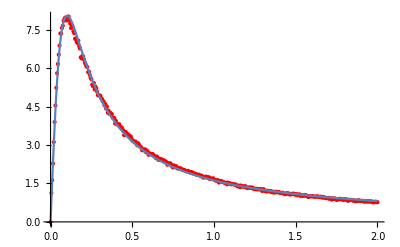

```mathematica
Show[ListPlot[v100,PlotStyle->Red],Plot[(a x)/(b (1+(x/b)^2))/.{a->16.088472477593466,b->0.10153461749000892},{x,0,2}]]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v200=blist[[3;;All,{14,6}]] 
FindFit[v200,a*(x/b)/(1+(x/b)^2),{a,b},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,2.38},{0.01,3.32},{0.015,5.17},{0.02,6.7},{0.025,8.37},{0.03,9.68},{0.035,11.27},{0.04,12.38},{0.045,13.4},{0.05,14.78},{0.055,15.66},{0.06,16.33},{0.065,17.02},{0.07,17.57},{0.075,18.2},{0.08,18.88},{0.085,18.83},{0.09,19.6},{0.095,19.82},{0.1,20.05},{0.105,19.27},{0.11,20.36},{0.115,20.13},{0.12,20.03},{0.125,20.28},{0.13,19.91},{0.135,20.18},{0.14,20.16},{0.145,20.05},{0.15,20.25},{0.155,20},{0.16,19.56},{0.165,19.67},{0.17,19.42},{0.175,19.32},{0.18,19.3},{0.185,18.83},{0.19,18.82},{0.195,18.63},{0.2,18.47},{0.205,18.32},{0.21,18.3},{0.215,17.87},{0.22,17.76},{0.225,17.81},{0.23,17.51},{0.235,17.66},{0.24,17.22},{0.245,17.15},{0.25,16.77},{0.255,16.87},{0.26,16.8},{0.265,16.38},{0.27,16.23},{0.275,16.22},{0.28,15.26},{0.285,15.48},{0.29,15.72},{0.295,15.26},{0.3,15.42},{0.305,15.2},{0.31,14.95},{0.315,14.7},{0.32,14.65},{0.325,14.87},{0.33,14.72},{0.335,14.3},{0.34,14.33},{0.345,14.06},{0.35,13.96},{0.355,14},{0.36,13.91},{0.365,13.76},{0.37,13.31},{0.375,13.3},{0.38,12.72},{0.385,12.97},{0.39,13.1},{0.395,13.1},{0.4,12.38},{0.405,12.51},{0.41,12.5},{0.415,12.55},{0.42,11.78},{0.425,12.17},{0.43,11.9},{0.435,11.85},{0.44,11.95},{0.445,11.86},{0.45,11.58},{0.455,11.33},{0.46,11.5},{0.465,11.26},{0.47,11.26},{0.475,11.16},{0.48,11.21},{0.485,11.13},{0.49,10.96},{0.495,10.85},{0.5,10.66},{0.505,10.76},{0.51,10.67},{0.515,10.5},{0.52,10.38},{0.525,10.21},{0.53,10.25},{0.535,10.01},{0.54,10.17},{0.545,9.82},{0.55,10.01},{0.555,9.88},{0.56,9.6},{0.565,9.73},{0.57,9.62},{0.575,9.51},{0.58,9.55},{0.585,9.58},{0.59,8.93},{0.595,9.3},{0.6,9.23},{0.605,9.2},{0.61,9.06},{0.615,9.15},{0.62,8.9},{0.625,8.86},{0.63,8.92},{0.635,8.88},{0.64,8.78},{0.645,8.78},{0.65,8.58},{0.655,8.36},{0.66,8.35},{0.665,8.41},{0.67,8.06},{0.675,8.42},{0.68,8.46},{0.685,8.18},{0.69,8.11},{0.695,8.11},{0.7,8.01},{0.705,7.76},{0.71,7.96},{0.715,7.98},{0.72,7.88},{0.725,7.71},{0.73,7.53},{0.735,7.67},{0.74,7.7},{0.745,7.58},{0.75,7.57},{0.755,7.51},{0.76,7.38},{0.765,7.4},{0.77,7.31},{0.775,7.21},{0.78,7.35},{0.785,7.27},{0.79,7.3},{0.795,7.25},{0.8,6.91},{0.805,7.05},{0.81,7.08},{0.815,6.98},{0.82,6.7},{0.825,6.98},{0.83,6.9},{0.835,6.92},{0.84,6.73},{0.845,6.67},{0.85,6.75},{0.855,6.72},{0.86,6.67},{0.865,6.78},{0.87,6.6},{0.875,6.67},{0.88,6.42},{0.885,6.47},{0.89,6.46},{0.895,6.43},{0.9,6.41},{0.905,6.36},{0.91,6.26},{0.915,6.32},{0.92,6.28},{0.925,6.37},{0.93,6.31},{0.935,6.2},{0.94,6.21},{0.945,6.11},{0.95,6.13},{0.955,6.13},{0.96,6},{0.965,6.05},{0.97,6.08},{0.975,6.01},{0.98,5.91},{0.985,5.81},{0.99,5.98},{0.995,5.71},{1,5.83},{1.005,5.75},{1.01,5.8},{1.015,5.75},{1.02,5.73},{1.025,5.63},{1.03,5.63},{1.035,5.62},{1.04,5.57},{1.045,5.43},{1.05,5.61},{1.055,5.43},{1.06,5.51},{1.065,5.51},{1.07,5.42},{1.075,5.47},{1.08,5.51},{1.085,5.28},{1.09,5.3},{1.095,5.31},{1.1,5.31},{1.105,5.28},{1.11,5.25},{1.115,5.28},{1.12,5.1},{1.125,5.15},{1.13,5.1},{1.135,5.1},{1.14,5.13},{1.145,5.16},{1.15,5.07},{1.155,5.08},{1.16,4.86},{1.165,4.96},{1.17,5.07},{1.175,4.95},{1.18,4.81},{1.185,4.91},{1.19,4.88},{1.195,4.83},{1.2,4.86},{1.205,4.61},{1.21,4.81},{1.215,4.8},{1.22,4.77},{1.225,4.81},{1.23,4.68},{1.235,4.73},{1.24,4.67},{1.245,4.66},{1.25,4.36},{1.255,4.6},{1.26,4.6},{1.265,4.55},{1.27,4.4},{1.275,4.55},{1.28,4.56},{1.285,4.4},{1.29,4.27},{1.295,4.37},{1.3,4.48},{1.305,4.37},{1.31,4.5},{1.315,4.36},{1.32,4.46},{1.325,4.38},{1.33,4.4},{1.335,4.36},{1.34,4.28},{1.345,4.31},{1.35,4.27},{1.355,4.16},{1.36,4.35},{1.365,4.22},{1.37,4.13},{1.375,4.2},{1.38,4.21},{1.385,4.12},{1.39,4.22},{1.395,4.18},{1.4,3.97},{1.405,4.13},{1.41,4.06},{1.415,4},{1.42,4.11},{1.425,4.1},{1.43,3.95},{1.435,4.03},{1.44,4.03},{1.445,4.07},{1.45,4.03},{1.455,4},{1.46,3.86},{1.465,3.93},{1.47,3.7},{1.475,3.88},{1.48,3.91},{1.485,3.86},{1.49,3.82},{1.495,3.86},{1.5,3.73},{1.505,3.75},{1.51,3.83},{1.515,3.82},{1.52,3.78},{1.525,3.82},{1.53,3.75},{1.535,3.61},{1.54,3.7},{1.545,3.55},{1.55,3.7},{1.555,3.66},{1.56,3.67},{1.565,3.61},{1.57,3.63},{1.575,3.63},{1.58,3.66},{1.585,3.6},{1.59,3.57},{1.595,3.61},{1.6,3.58},{1.605,3.57},{1.61,3.52},{1.615,3.58},{1.62,3.55},{1.625,3.53},{1.63,3.5},{1.635,3.53},{1.64,3.45},{1.645,3.42},{1.65,3.47},{1.655,3.35},{1.66,3.42},{1.665,3.43},{1.67,3.46},{1.675,3.37},{1.68,3.36},{1.685,3.4},{1.69,3.38},{1.695,3.36},{1.7,3.23},{1.705,3.21},{1.71,3.32},{1.715,3.3},{1.72,3.27},{1.725,3.27},{1.73,3.27},{1.735,3.28},{1.74,3.25},{1.745,3.12},{1.75,3.18},{1.755,3.17},{1.76,3.25},{1.765,3.23},{1.77,3.16},{1.775,3.16},{1.78,3.2},{1.785,3.18},{1.79,3.18},{1.795,3.12},{1.8,3.13},{1.805,3.1},{1.81,3.08},{1.815,3.11},{1.82,3.02},{1.825,2.93},{1.83,2.9},{1.835,2.91},{1.84,3.06},{1.845,3.03},{1.85,3.02},{1.855,3},{1.86,2.97},{1.865,2.98},{1.87,2.93},{1.875,3.06},{1.88,3},{1.885,2.96},{1.89,2.97},{1.895,2.9},{1.9,2.86},{1.905,2.97},{1.91,3},{1.915,2.97},{1.92,2.92},{1.925,2.96},{1.93,2.92},{1.935,2.88},{1.94,2.92},{1.945,2.95},{1.95,2.9},{1.955,2.85},{1.96,2.9},{1.965,2.9},{1.97,2.87},{1.975,2.87},{1.98,2.82},{1.985,2.83},{1.99,2.83},{1.995,2.83},{2,2.85}}

{a→41.5353,b→0.135976}

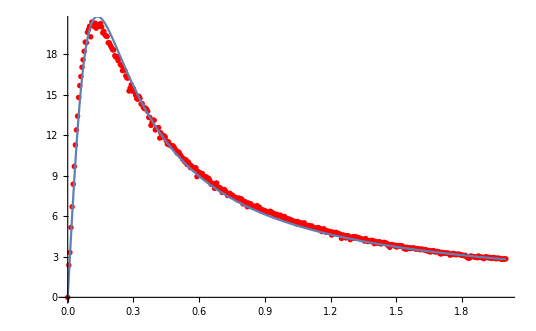

```mathematica
Show[ListPlot[v200,PlotStyle->Red],Plot[(a x)/(b (1+(x/b)^2))/.{a->41.53528980870369,b->0.1359759469052245},{x,0,2}]]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v400=blist[[3;;All,{14,7}]] 
FindFit[v400,a*(x/b)/(1+(x/b)^2),{a,b},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,4.13},{0.01,5.93},{0.015,8.68},{0.02,11.63},{0.025,14.8},{0.03,17.3},{0.035,20},{0.04,22.23},{0.045,24.15},{0.05,27.23},{0.055,28.85},{0.06,30.25},{0.065,32.88},{0.07,33.28},{0.075,35.55},{0.08,35.9},{0.085,37.03},{0.09,37.13},{0.095,37.6},{0.1,40.03},{0.105,40.58},{0.11,41.55},{0.115,41.25},{0.12,41.2},{0.125,42.33},{0.13,41.88},{0.135,42.7},{0.14,43.03},{0.145,43.13},{0.15,43.4},{0.155,43.43},{0.16,44.15},{0.165,44.05},{0.17,43.78},{0.175,43.38},{0.18,44.1},{0.185,44.5},{0.19,42.68},{0.195,43.2},{0.2,43.35},{0.205,43.5},{0.21,43.75},{0.215,41.95},{0.22,42.95},{0.225,42.7},{0.23,42.5},{0.235,40.98},{0.24,42.23},{0.245,41.9},{0.25,42.6},{0.255,42.43},{0.26,41.85},{0.265,41.3},{0.27,41.45},{0.275,41.03},{0.28,41.23},{0.285,40.85},{0.29,38.9},{0.295,40.13},{0.3,40.6},{0.305,39.55},{0.31,39.38},{0.315,39.58},{0.32,38.93},{0.325,38.85},{0.33,38.33},{0.335,38.58},{0.34,38.48},{0.345,36.7},{0.35,36.65},{0.355,37.18},{0.36,36.08},{0.365,36.98},{0.37,35.93},{0.375,36.08},{0.38,35.53},{0.385,35.83},{0.39,35.73},{0.395,35.93},{0.4,35.55},{0.405,34.45},{0.41,34.78},{0.415,35.13},{0.42,34.55},{0.425,34.73},{0.43,33.8},{0.435,33.58},{0.44,33.48},{0.445,32.4},{0.45,33.1},{0.455,31.93},{0.46,32.63},{0.465,33.1},{0.47,32.4},{0.475,32.03},{0.48,30.78},{0.485,30.4},{0.49,31.43},{0.495,31.15},{0.5,30.08},{0.505,30.33},{0.51,30.83},{0.515,29.35},{0.52,30.23},{0.525,29.8},{0.53,29.9},{0.535,29.7},{0.54,29.8},{0.545,29.88},{0.55,29.18},{0.555,28.93},{0.56,28.98},{0.565,28.25},{0.57,28.55},{0.575,28.35},{0.58,28.15},{0.585,27.85},{0.59,27.78},{0.595,26.8},{0.6,27.55},{0.605,27.08},{0.61,27.4},{0.615,26.95},{0.62,26.6},{0.625,26.78},{0.63,26.58},{0.635,26.55},{0.64,26.55},{0.645,25.65},{0.65,25.93},{0.655,25.9},{0.66,25.8},{0.665,25.1},{0.67,25.18},{0.675,25.15},{0.68,24},{0.685,24.9},{0.69,24.58},{0.695,24.73},{0.7,24.4},{0.705,24.53},{0.71,24.8},{0.715,24.03},{0.72,24.35},{0.725,22.33},{0.73,23.98},{0.735,22.98},{0.74,23.45},{0.745,23.3},{0.75,23.63},{0.755,23.15},{0.76,23.18},{0.765,22.2},{0.77,22.83},{0.775,23.08},{0.78,23.18},{0.785,22.7},{0.79,22.15},{0.795,22.53},{0.8,21.88},{0.805,21.75},{0.81,22.3},{0.815,21.68},{0.82,22.03},{0.825,22.2},{0.83,20.73},{0.835,20.95},{0.84,21.28},{0.845,21.48},{0.85,21.55},{0.855,21.25},{0.86,21.03},{0.865,21.1},{0.87,20.88},{0.875,20.13},{0.88,20.6},{0.885,20.03},{0.89,20.45},{0.895,20.58},{0.9,19.58},{0.905,20.05},{0.91,20.33},{0.915,20.2},{0.92,19.8},{0.925,19.2},{0.93,19.43},{0.935,18.9},{0.94,19.48},{0.945,19.58},{0.95,19.4},{0.955,19.3},{0.96,19.28},{0.965,19.03},{0.97,18.6},{0.975,19.13},{0.98,18.78},{0.985,19.05},{0.99,19.1},{0.995,19.03},{1,18.6},{1.005,18.55},{1.01,18.23},{1.015,17.85},{1.02,18.1},{1.025,17.88},{1.03,18.03},{1.035,17.43},{1.04,17.88},{1.045,17.9},{1.05,17.9},{1.055,17.4},{1.06,17.45},{1.065,17.53},{1.07,17.65},{1.075,17.33},{1.08,16.7},{1.085,17.23},{1.09,17.38},{1.095,17.05},{1.1,17.08},{1.105,17.15},{1.11,17.05},{1.115,16.83},{1.12,16.33},{1.125,15.65},{1.13,16.38},{1.135,16.63},{1.14,16.58},{1.145,15.63},{1.15,16.28},{1.155,16.55},{1.16,16.18},{1.165,15.98},{1.17,16.13},{1.175,15.88},{1.18,15.3},{1.185,15.98},{1.19,16.13},{1.195,16.05},{1.2,15.63},{1.205,15.68},{1.21,15.7},{1.215,15.7},{1.22,15.48},{1.225,15.58},{1.23,15.23},{1.235,15.33},{1.24,15.48},{1.245,15.15},{1.25,14.68},{1.255,14.93},{1.26,14.98},{1.265,14.98},{1.27,14.93},{1.275,14.7},{1.28,14.85},{1.285,14.65},{1.29,14.75},{1.295,14.55},{1.3,14.53},{1.305,14.63},{1.31,14.55},{1.315,14.53},{1.32,14.55},{1.325,14.15},{1.33,14.38},{1.335,14.3},{1.34,14.23},{1.345,14},{1.35,14.2},{1.355,13.85},{1.36,14.13},{1.365,13.78},{1.37,13.85},{1.375,13.8},{1.38,13.8},{1.385,13.7},{1.39,13.63},{1.395,13.5},{1.4,13.18},{1.405,13.53},{1.41,13.48},{1.415,13.23},{1.42,13.48},{1.425,13.38},{1.43,13.15},{1.435,12.8},{1.44,13.2},{1.445,13.15},{1.45,12.73},{1.455,12.5},{1.46,12.95},{1.465,13.08},{1.47,13.03},{1.475,12.95},{1.48,13.05},{1.485,12.85},{1.49,12.75},{1.495,12.93},{1.5,12.68},{1.505,12.58},{1.51,12.78},{1.515,12.68},{1.52,12.6},{1.525,12.6},{1.53,12.48},{1.535,12.43},{1.54,12.43},{1.545,12.48},{1.55,12.45},{1.555,12.33},{1.56,12.23},{1.565,12.1},{1.57,11.98},{1.575,12.05},{1.58,11.88},{1.585,11.38},{1.59,11.95},{1.595,12},{1.6,11.98},{1.605,11.88},{1.61,11.68},{1.615,11.9},{1.62,12.03},{1.625,11.75},{1.63,11.7},{1.635,11.3},{1.64,11.55},{1.645,11.6},{1.65,11.1},{1.655,11.43},{1.66,11.13},{1.665,11.38},{1.67,11.45},{1.675,11.33},{1.68,11.3},{1.685,11.43},{1.69,11.53},{1.695,11.3},{1.7,11.33},{1.705,11.25},{1.71,11.13},{1.715,11.3},{1.72,10.83},{1.725,10.98},{1.73,11.23},{1.735,11.05},{1.74,10.83},{1.745,10.85},{1.75,10.88},{1.755,10.83},{1.76,10.83},{1.765,10.98},{1.77,10.95},{1.775,10.78},{1.78,10.88},{1.785,10.65},{1.79,10.78},{1.795,10.65},{1.8,10.55},{1.805,10.43},{1.81,10.25},{1.815,10.08},{1.82,10.38},{1.825,10.55},{1.83,10.65},{1.835,10.55},{1.84,10.58},{1.845,10.48},{1.85,10.25},{1.855,9.85},{1.86,9.9},{1.865,10.25},{1.87,10.15},{1.875,10.18},{1.88,10},{1.885,10.1},{1.89,10.15},{1.895,10.08},{1.9,10.03},{1.905,9.93},{1.91,10.08},{1.915,10.1},{1.92,10.1},{1.925,9.93},{1.93,10},{1.935,10},{1.94,9.83},{1.945,9.4},{1.95,9.75},{1.955,9.58},{1.96,9.75},{1.965,9.8},{1.97,9.33},{1.975,9.53},{1.98,9.55},{1.985,9.75},{1.99,9.23},{1.995,9.48},{2,9.43}}

{a→91.7309,b→0.197329}

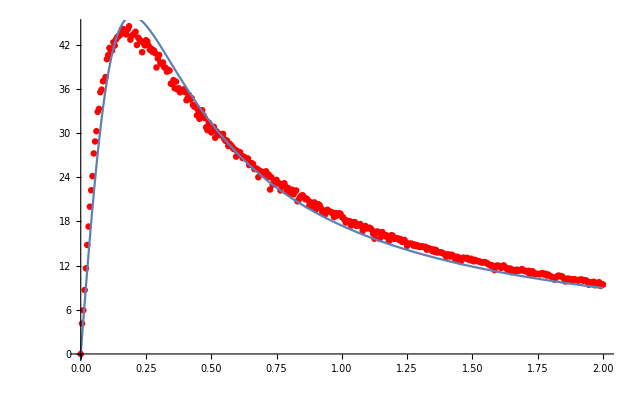

```mathematica
Show[ListPlot[v400,PlotStyle->Red],Plot[(a x)/(b (1+(x/b)^2))/.{a->91.73090137346854,b->0.19732939733914662},{x,0,2}]]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v600=blist[[3;;All,{14,8}]] 
FindFit[v600,a*(x/b-r)/(1+(x/b)^2),{a,b,r},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,5.08},{0.01,7.15},{0.015,10.65},{0.02,13.85},{0.025,18.05},{0.03,21.95},{0.035,24.33},{0.04,27.85},{0.045,30.9},{0.05,34.45},{0.055,36.63},{0.06,38.4},{0.065,41.35},{0.07,43.05},{0.075,43.55},{0.08,46.48},{0.085,48.63},{0.09,49.93},{0.095,51.38},{0.1,53.13},{0.105,53.93},{0.11,55.13},{0.115,55.2},{0.12,56.08},{0.125,58.48},{0.13,58.03},{0.135,59.3},{0.14,60.03},{0.145,58.93},{0.15,61.05},{0.155,61.93},{0.16,60.55},{0.165,63.03},{0.17,63.1},{0.175,62.45},{0.18,63.58},{0.185,64.33},{0.19,62.5},{0.195,63.65},{0.2,63.73},{0.205,63.43},{0.21,64.15},{0.215,63.73},{0.22,64.38},{0.225,64.55},{0.23,62.9},{0.235,64.15},{0.24,63.15},{0.245,63.6},{0.25,64.38},{0.255,63.43},{0.26,63.95},{0.265,64.58},{0.27,65.23},{0.275,63.23},{0.28,63.4},{0.285,63.9},{0.29,64.1},{0.295,61.2},{0.3,63.48},{0.305,62.28},{0.31,61.98},{0.315,62.93},{0.32,62.45},{0.325,62.33},{0.33,62.03},{0.335,61.45},{0.34,62.05},{0.345,60.75},{0.35,58.18},{0.355,60.83},{0.36,60.85},{0.365,60.95},{0.37,59.68},{0.375,59.53},{0.38,60.48},{0.385,59.7},{0.39,60.13},{0.395,59.68},{0.4,58.78},{0.405,58.68},{0.41,57.65},{0.415,56.98},{0.42,57.83},{0.425,57.75},{0.43,56.53},{0.435,57.8},{0.44,56.95},{0.445,56.53},{0.45,56.2},{0.455,55.73},{0.46,55.68},{0.465,55.18},{0.47,53.4},{0.475,54.35},{0.48,54.35},{0.485,55.38},{0.49,54.08},{0.495,52.43},{0.5,53.6},{0.505,51.68},{0.51,54.1},{0.515,52.65},{0.52,53.08},{0.525,51.18},{0.53,51.75},{0.535,51.83},{0.54,52.6},{0.545,50.78},{0.55,51.05},{0.555,50.95},{0.56,49.18},{0.565,50.1},{0.57,50.38},{0.575,50.6},{0.58,49.75},{0.585,49.83},{0.59,50.38},{0.595,48.55},{0.6,48.63},{0.605,48.83},{0.61,48.7},{0.615,47.95},{0.62,45.55},{0.625,47.28},{0.63,48.08},{0.635,47.95},{0.64,47.7},{0.645,47.75},{0.65,46.55},{0.655,46.2},{0.66,45.55},{0.665,46.58},{0.67,46.65},{0.675,44.55},{0.68,45.05},{0.685,45.93},{0.69,44.93},{0.695,45.15},{0.7,45.33},{0.705,45.03},{0.71,44.78},{0.715,42.4},{0.72,44.15},{0.725,43.55},{0.73,43.18},{0.735,42.93},{0.74,43.6},{0.745,43.58},{0.75,43.98},{0.755,42.13},{0.76,42.43},{0.765,41.93},{0.77,41.38},{0.775,41.75},{0.78,40.5},{0.785,41.25},{0.79,41},{0.795,40.68},{0.8,40.83},{0.805,40.78},{0.81,40.4},{0.815,41.03},{0.82,40.05},{0.825,40.2},{0.83,40.83},{0.835,40.25},{0.84,39.83},{0.845,40.33},{0.85,39.6},{0.855,38.9},{0.86,39.18},{0.865,38.95},{0.87,38.68},{0.875,37.88},{0.88,38},{0.885,38.5},{0.89,38},{0.895,38.5},{0.9,38},{0.905,37.73},{0.91,37.8},{0.915,36},{0.92,35.25},{0.925,37.03},{0.93,37.38},{0.935,37},{0.94,36.3},{0.945,37},{0.95,36.35},{0.955,35.43},{0.96,36.18},{0.965,34.58},{0.97,35.68},{0.975,35.98},{0.98,36.05},{0.985,36.25},{0.99,35.5},{0.995,35.28},{1,34.95},{1.005,35.28},{1.01,34.95},{1.015,34},{1.02,33},{1.025,33.83},{1.03,34.63},{1.035,34.03},{1.04,34.05},{1.045,33.55},{1.05,32.38},{1.055,33.2},{1.06,33.35},{1.065,33.78},{1.07,33.15},{1.075,32.78},{1.08,33.1},{1.085,32.75},{1.09,32.95},{1.095,32.4},{1.1,33.03},{1.105,32.73},{1.11,32.78},{1.115,32.23},{1.12,32.7},{1.125,32.25},{1.13,31.83},{1.135,32},{1.14,32},{1.145,30.2},{1.15,31.23},{1.155,30.98},{1.16,29.93},{1.165,31.05},{1.17,30.43},{1.175,30.45},{1.18,31.03},{1.185,30.73},{1.19,30.98},{1.195,30.75},{1.2,30.65},{1.205,30.63},{1.21,29.3},{1.215,29.13},{1.22,30.35},{1.225,29.38},{1.23,29.45},{1.235,28.5},{1.24,29.08},{1.245,28.95},{1.25,29.43},{1.255,28.25},{1.26,29.28},{1.265,28.83},{1.27,29.08},{1.275,28.98},{1.28,28.4},{1.285,28.65},{1.29,27.9},{1.295,28.4},{1.3,28.45},{1.305,28.25},{1.31,28.25},{1.315,27.65},{1.32,28.2},{1.325,28.03},{1.33,27.68},{1.335,28.08},{1.34,28.05},{1.345,27.7},{1.35,27.35},{1.355,27.33},{1.36,27.05},{1.365,26.85},{1.37,25.88},{1.375,26.48},{1.38,25.9},{1.385,25.95},{1.39,26.28},{1.395,26.98},{1.4,26.38},{1.405,25.93},{1.41,26.4},{1.415,26.38},{1.42,26.05},{1.425,26.18},{1.43,25.88},{1.435,26.13},{1.44,25.03},{1.445,25.2},{1.45,25.43},{1.455,25.48},{1.46,25.7},{1.465,25.35},{1.47,25.43},{1.475,25.05},{1.48,25.43},{1.485,25.55},{1.49,24.85},{1.495,24.85},{1.5,24.35},{1.505,23.68},{1.51,24.88},{1.515,23.73},{1.52,24.43},{1.525,24.1},{1.53,23.78},{1.535,24.2},{1.54,24.25},{1.545,23.98},{1.55,24.38},{1.555,24.1},{1.56,24.3},{1.565,24.08},{1.57,24.23},{1.575,24.05},{1.58,23.78},{1.585,23.05},{1.59,23.35},{1.595,23.23},{1.6,23.35},{1.605,23.33},{1.61,23.13},{1.615,23.15},{1.62,23.13},{1.625,23.4},{1.63,23.03},{1.635,23.18},{1.64,23.18},{1.645,22.85},{1.65,22.05},{1.655,22.68},{1.66,22.43},{1.665,22.2},{1.67,22.4},{1.675,22.15},{1.68,22.1},{1.685,22.35},{1.69,22.25},{1.695,21.98},{1.7,21.85},{1.705,22.13},{1.71,21.88},{1.715,21.7},{1.72,22.13},{1.725,20.95},{1.73,20.98},{1.735,20.8},{1.74,21.35},{1.745,21.88},{1.75,21.73},{1.755,21.2},{1.76,21.4},{1.765,20.63},{1.77,21.5},{1.775,21.65},{1.78,21.33},{1.785,21.18},{1.79,20.8},{1.795,21.23},{1.8,21.25},{1.805,20.85},{1.81,20.63},{1.815,19.95},{1.82,20.68},{1.825,21.05},{1.83,20.8},{1.835,19.93},{1.84,20.78},{1.845,19.73},{1.85,20.05},{1.855,20.23},{1.86,19.65},{1.865,20.4},{1.87,20.43},{1.875,20.2},{1.88,20.43},{1.885,20},{1.89,20.28},{1.895,19.18},{1.9,19.65},{1.905,20.2},{1.91,20.13},{1.915,19.98},{1.92,19.5},{1.925,19.55},{1.93,19.38},{1.935,19.5},{1.94,19.6},{1.945,19.3},{1.95,19.13},{1.955,19.5},{1.96,19.25},{1.965,18.95},{1.97,19.25},{1.975,18.55},{1.98,18.85},{1.985,19.25},{1.99,18.68},{1.995,19},{2,19.13}}

{a→120.446,b→0.296992,r→-0.094447}

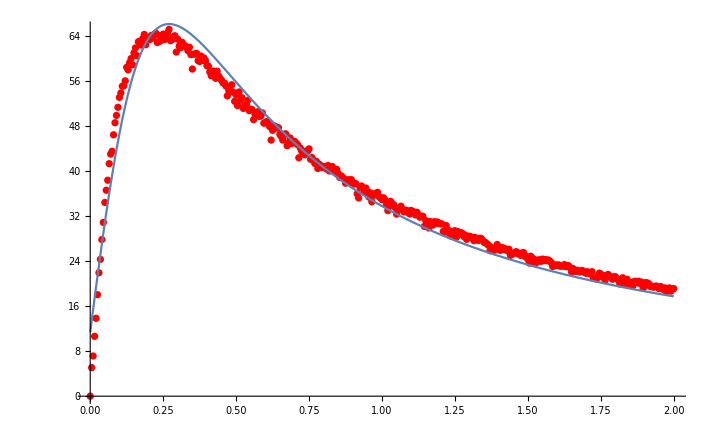

```mathematica
Show[ListPlot[v600,PlotStyle->Red],Plot[(a (x/b-r))/(1+(x/b)^2)/.{a->120.4460738248475,b->0.29699221783550156,r->-0.09444704909714932},{x,0,2}]]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v800=blist[[3;;All,{14,9}]] 
FindFit[v800,a*(x/b-r)/(1+(x/b)^2),{a,b,r},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,5.4},{0.01,8.05},{0.015,11.85},{0.02,15.4},{0.025,19.8},{0.03,24},{0.035,27.4},{0.04,30.8},{0.045,34.35},{0.05,37.95},{0.055,40.85},{0.06,44.1},{0.065,47},{0.07,49.3},{0.075,52},{0.08,53.75},{0.085,54.6},{0.09,57.3},{0.095,58.05},{0.1,60.7},{0.105,62.1},{0.11,63.75},{0.115,65.05},{0.12,66.25},{0.125,68.25},{0.13,68.65},{0.135,69.75},{0.14,70.45},{0.145,71.15},{0.15,71.05},{0.155,71.75},{0.16,73.6},{0.165,74.7},{0.17,76},{0.175,73.5},{0.18,76.6},{0.185,77.15},{0.19,77.3},{0.195,77.35},{0.2,78.65},{0.205,77.75},{0.21,78.6},{0.215,78.9},{0.22,79.25},{0.225,80.6},{0.23,79.6},{0.235,79.45},{0.24,79.8},{0.245,80.7},{0.25,79.9},{0.255,80},{0.26,79.7},{0.265,78.65},{0.27,80.3},{0.275,80.6},{0.28,80.75},{0.285,80.3},{0.29,78.85},{0.295,79.85},{0.3,79},{0.305,81.15},{0.31,80},{0.315,80.85},{0.32,79.6},{0.325,79.65},{0.33,78.65},{0.335,76.8},{0.34,78.4},{0.345,78.8},{0.35,79.2},{0.355,78.75},{0.36,78.05},{0.365,75.6},{0.37,78.9},{0.375,78.5},{0.38,78.85},{0.385,78.45},{0.39,77.45},{0.395,76.9},{0.4,77.95},{0.405,78.15},{0.41,77},{0.415,74},{0.42,76},{0.425,76},{0.43,77.15},{0.435,76.45},{0.44,75.65},{0.445,75.15},{0.45,75.55},{0.455,75.05},{0.46,74.4},{0.465,75.15},{0.47,74},{0.475,74.4},{0.48,72.6},{0.485,73.75},{0.49,74.5},{0.495,73.05},{0.5,72.3},{0.505,72.6},{0.51,68.95},{0.515,71.4},{0.52,69.25},{0.525,71.65},{0.53,70.85},{0.535,71},{0.54,70.85},{0.545,70.25},{0.55,69.55},{0.555,70.25},{0.56,69.4},{0.565,67.7},{0.57,69.2},{0.575,69.35},{0.58,69.4},{0.585,65.65},{0.59,64.95},{0.595,68.45},{0.6,68.2},{0.605,67.5},{0.61,65.35},{0.615,65.65},{0.62,66.1},{0.625,67.7},{0.63,66.05},{0.635,65.55},{0.64,65.65},{0.645,64.9},{0.65,64},{0.655,64.85},{0.66,63.3},{0.665,63.6},{0.67,64.05},{0.675,63.95},{0.68,62.1},{0.685,64.25},{0.69,64.65},{0.695,62.7},{0.7,62.4},{0.705,61.5},{0.71,62.45},{0.715,62.8},{0.72,61.8},{0.725,61.05},{0.73,59.85},{0.735,60.5},{0.74,60.75},{0.745,60.55},{0.75,60.7},{0.755,60.45},{0.76,60.1},{0.765,58},{0.77,59.15},{0.775,60.15},{0.78,58.05},{0.785,58.6},{0.79,58.9},{0.795,59.25},{0.8,59.45},{0.805,58.2},{0.81,57.6},{0.815,58.35},{0.82,58.2},{0.825,58},{0.83,58},{0.835,58},{0.84,57.1},{0.845,54.15},{0.85,56.45},{0.855,56.05},{0.86,56.1},{0.865,55.7},{0.87,56.45},{0.875,54.75},{0.88,54.85},{0.885,53.55},{0.89,53.3},{0.895,54.2},{0.9,54.25},{0.905,54.4},{0.91,53.9},{0.915,51.7},{0.92,53.35},{0.925,53.4},{0.93,52.1},{0.935,53.85},{0.94,52.15},{0.945,53.6},{0.95,51},{0.955,52.25},{0.96,50.85},{0.965,52.45},{0.97,52.1},{0.975,52.05},{0.98,52.35},{0.985,49.75},{0.99,51.4},{0.995,50.85},{1,50.35},{1.005,51.1},{1.01,50.45},{1.015,49.2},{1.02,50.3},{1.025,50.35},{1.03,49},{1.035,48.15},{1.04,49.75},{1.045,48.9},{1.05,48.85},{1.055,49.25},{1.06,47.6},{1.065,46.95},{1.07,47.95},{1.075,48.1},{1.08,47.55},{1.085,48.4},{1.09,48.4},{1.095,48.45},{1.1,46.1},{1.105,46},{1.11,47},{1.115,47.4},{1.12,45.9},{1.125,46.95},{1.13,46.7},{1.135,46.5},{1.14,45.8},{1.145,45.6},{1.15,46.15},{1.155,46.75},{1.16,44.1},{1.165,45.15},{1.17,45.3},{1.175,45.1},{1.18,45.05},{1.185,45.75},{1.19,44.9},{1.195,45.15},{1.2,45.05},{1.205,44.8},{1.21,44},{1.215,44.65},{1.22,43.85},{1.225,44.3},{1.23,44.4},{1.235,44.15},{1.24,43.1},{1.245,43.55},{1.25,41.8},{1.255,43.15},{1.26,42.55},{1.265,43},{1.27,41},{1.275,42.2},{1.28,41.9},{1.285,41.9},{1.29,41.85},{1.295,41.65},{1.3,42.25},{1.305,41.95},{1.31,41.15},{1.315,40.75},{1.32,41.45},{1.325,41.25},{1.33,40.35},{1.335,40.4},{1.34,41.45},{1.345,41.25},{1.35,40.95},{1.355,41.15},{1.36,39.5},{1.365,40.25},{1.37,40},{1.375,40.55},{1.38,39.85},{1.385,39.9},{1.39,39.8},{1.395,38.55},{1.4,39.05},{1.405,39.85},{1.41,39},{1.415,39.15},{1.42,39.7},{1.425,39.35},{1.43,38.85},{1.435,38.8},{1.44,39.15},{1.445,36.9},{1.45,38.6},{1.455,38.25},{1.46,38.25},{1.465,36.65},{1.47,38.3},{1.475,36.8},{1.48,35.55},{1.485,37.6},{1.49,37.7},{1.495,37.55},{1.5,37.55},{1.505,37.55},{1.51,36.65},{1.515,37.35},{1.52,36.8},{1.525,36.3},{1.53,36.5},{1.535,36.15},{1.54,36.2},{1.545,35.85},{1.55,36},{1.555,36.35},{1.56,36.3},{1.565,36.1},{1.57,34.4},{1.575,34.45},{1.58,33.9},{1.585,35.85},{1.59,35.9},{1.595,35.35},{1.6,35.3},{1.605,35.25},{1.61,35.5},{1.615,35.3},{1.62,33.8},{1.625,35},{1.63,34.55},{1.635,34.4},{1.64,33.6},{1.645,34.2},{1.65,34.7},{1.655,34.1},{1.66,33.85},{1.665,34.3},{1.67,34.25},{1.675,32.5},{1.68,33.3},{1.685,33.1},{1.69,33.5},{1.695,33.65},{1.7,33.55},{1.705,33.55},{1.71,33.4},{1.715,33.65},{1.72,33.6},{1.725,32.5},{1.73,32.6},{1.735,32.5},{1.74,33.3},{1.745,32.85},{1.75,32.55},{1.755,32.5},{1.76,32.4},{1.765,32.35},{1.77,32.35},{1.775,31.35},{1.78,32.35},{1.785,32.1},{1.79,31.7},{1.795,32.15},{1.8,32.35},{1.805,31.7},{1.81,32.2},{1.815,31.55},{1.82,31.3},{1.825,30.9},{1.83,31.1},{1.835,31.35},{1.84,31.35},{1.845,30.75},{1.85,29.7},{1.855,30.8},{1.86,31.35},{1.865,30.8},{1.87,30.85},{1.875,31},{1.88,30.45},{1.885,30.35},{1.89,30.25},{1.895,30.7},{1.9,30.15},{1.905,30.7},{1.91,30.75},{1.915,29.95},{1.92,30.4},{1.925,30.1},{1.93,30},{1.935,29.8},{1.94,30.1},{1.945,29.35},{1.95,28.1},{1.955,29.1},{1.96,29.5},{1.965,29.35},{1.97,28.05},{1.975,29},{1.98,29.6},{1.985,28.65},{1.99,29.2},{1.995,27.85},{2,28.6}}

{a→148.33,b→0.365191,r→-0.109589}

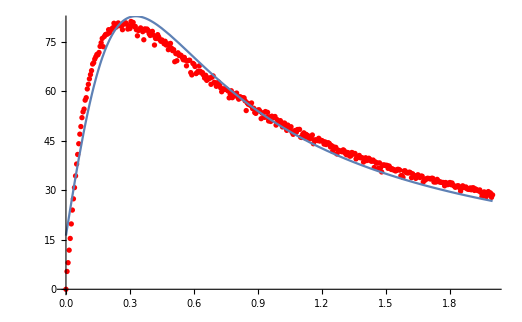

```mathematica
Show[ListPlot[v800,PlotStyle->Red],Plot[(a (x/b-r))/(1+(x/b)^2)/.{a->148.3295172128415,b->0.3651909330728809,r->-0.10958898700943073},{x,0,2}]]
```

## Manipulate

```mathematica
Manipulate[Show[Plot[(a (x/b-r))/(1+(x/b)^2),{x,0,2},PlotRange->All],ListPlot[v800]],{a,0,500},{b,000.1,2},{r,-10,10}]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v1000=blist[[3;;All,{14,10}]] 
FindFit[v1000,a*(x/b-r)/(1+(x/b)^2),{a,b,r},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,5.8},{0.01,8.2},{0.015,12.75},{0.02,17},{0.025,20.9},{0.03,25.3},{0.035,29.6},{0.04,32.8},{0.045,35.75},{0.05,41},{0.055,44.1},{0.06,47.6},{0.065,50.85},{0.07,53.9},{0.075,57.35},{0.08,58.15},{0.085,61.55},{0.09,62.75},{0.095,67.95},{0.1,69.95},{0.105,70.7},{0.11,72.45},{0.115,72.85},{0.12,75.55},{0.125,79.4},{0.13,78.8},{0.135,80.35},{0.14,82.7},{0.145,82.9},{0.15,84.6},{0.155,83.65},{0.16,84.05},{0.165,86.45},{0.17,88.9},{0.175,89.85},{0.18,88.8},{0.185,91.85},{0.19,92.3},{0.195,93.05},{0.2,93.15},{0.205,95.6},{0.21,94.65},{0.215,96.75},{0.22,95.3},{0.225,97.15},{0.23,99.1},{0.235,98.45},{0.24,99.1},{0.245,99.95},{0.25,98.75},{0.255,99.2},{0.26,100.7},{0.265,100},{0.27,101.15},{0.275,100.9},{0.28,102.3},{0.285,100.75},{0.29,103.1},{0.295,103.35},{0.3,102.05},{0.305,103.35},{0.31,101.95},{0.315,103.7},{0.32,98.85},{0.325,101.8},{0.33,101.25},{0.335,104},{0.34,101.8},{0.345,101.8},{0.35,102.5},{0.355,103.5},{0.36,103.4},{0.365,100.85},{0.37,102.55},{0.375,100.3},{0.38,102.5},{0.385,103.7},{0.39,103.15},{0.395,101.85},{0.4,100.45},{0.405,102.15},{0.41,101.9},{0.415,99.75},{0.42,102.5},{0.425,102.9},{0.43,101.25},{0.435,102.25},{0.44,100.75},{0.445,103.1},{0.45,101.65},{0.455,101.2},{0.46,99.6},{0.465,100.2},{0.47,101.35},{0.475,99.85},{0.48,99},{0.485,101.25},{0.49,100.7},{0.495,101.35},{0.5,99.05},{0.505,100.1},{0.51,101.3},{0.515,98.25},{0.52,98.9},{0.525,99.95},{0.53,99.65},{0.535,98.4},{0.54,97.85},{0.545,99.65},{0.55,95.8},{0.555,98.5},{0.56,97.3},{0.565,94.65},{0.57,96.25},{0.575,96.75},{0.58,95.35},{0.585,96.65},{0.59,97.15},{0.595,94.6},{0.6,96.45},{0.605,94.35},{0.61,94.5},{0.615,95.65},{0.62,94.35},{0.625,94.35},{0.63,92.75},{0.635,92.8},{0.64,95.25},{0.645,94.65},{0.65,94.25},{0.655,93.2},{0.66,93.45},{0.665,93.5},{0.67,92.5},{0.675,87.05},{0.68,92.8},{0.685,88.3},{0.69,91.15},{0.695,91.65},{0.7,89.25},{0.705,86.6},{0.71,90.65},{0.715,89.7},{0.72,90.85},{0.725,86.8},{0.73,85.45},{0.735,87.3},{0.74,87.1},{0.745,87.3},{0.75,87.95},{0.755,85.3},{0.76,87.05},{0.765,84.05},{0.77,88.05},{0.775,88.75},{0.78,86.4},{0.785,86.55},{0.79,87.7},{0.795,86},{0.8,84.2},{0.805,85.95},{0.81,86.4},{0.815,84.85},{0.82,84.85},{0.825,82.35},{0.83,83.45},{0.835,85.55},{0.84,85.65},{0.845,85.4},{0.85,83.8},{0.855,83.8},{0.86,84.5},{0.865,84.75},{0.87,82.5},{0.875,82.9},{0.88,83.95},{0.885,83.35},{0.89,82.95},{0.895,83.15},{0.9,82.5},{0.905,82.95},{0.91,82.35},{0.915,80.2},{0.92,80.95},{0.925,81.1},{0.93,79.9},{0.935,79.95},{0.94,80.3},{0.945,78.1},{0.95,80},{0.955,80.4},{0.96,79.45},{0.965,78.3},{0.97,77.7},{0.975,77.55},{0.98,75.15},{0.985,77.2},{0.99,78.6},{0.995,79.25},{1,76.2},{1.005,77.85},{1.01,77.2},{1.015,76.65},{1.02,74.15},{1.025,76.95},{1.03,73.45},{1.035,74.3},{1.04,73.75},{1.045,74.75},{1.05,75.95},{1.055,75.8},{1.06,75},{1.065,71.95},{1.07,74.95},{1.075,74.5},{1.08,74.1},{1.085,71.15},{1.09,74},{1.095,74.35},{1.1,72.1},{1.105,71.1},{1.11,71.9},{1.115,72.8},{1.12,72.55},{1.125,73},{1.13,72.2},{1.135,71.8},{1.14,71.7},{1.145,72.55},{1.15,71.35},{1.155,71.75},{1.16,71.35},{1.165,70.4},{1.17,69.15},{1.175,69.85},{1.18,69.55},{1.185,69.6},{1.19,68.2},{1.195,68.1},{1.2,69},{1.205,68.85},{1.21,69.95},{1.215,69.75},{1.22,68.75},{1.225,65.9},{1.23,67.5},{1.235,67.1},{1.24,67},{1.245,66.25},{1.25,68},{1.255,68},{1.26,64.95},{1.265,67.7},{1.27,65.55},{1.275,65.95},{1.28,66.25},{1.285,66.95},{1.29,64.5},{1.295,65.1},{1.3,66.25},{1.305,65.25},{1.31,66.2},{1.315,65.35},{1.32,65.95},{1.325,64.65},{1.33,63.55},{1.335,64.7},{1.34,65.25},{1.345,65},{1.35,63.1},{1.355,63.25},{1.36,64.55},{1.365,64.2},{1.37,63.4},{1.375,64.35},{1.38,62.9},{1.385,63.85},{1.39,63.15},{1.395,61.55},{1.4,61.7},{1.405,62.25},{1.41,61.9},{1.415,61.9},{1.42,62.9},{1.425,59.95},{1.43,61.7},{1.435,60.7},{1.44,62.05},{1.445,58.75},{1.45,61},{1.455,58.45},{1.46,58.4},{1.465,60.8},{1.47,60.7},{1.475,58.8},{1.48,57.95},{1.485,58.95},{1.49,59},{1.495,59.25},{1.5,56.65},{1.505,59.7},{1.51,59.05},{1.515,59.9},{1.52,59},{1.525,59.7},{1.53,57.25},{1.535,57.9},{1.54,57.3},{1.545,58.3},{1.55,59.1},{1.555,58.75},{1.56,57.6},{1.565,58.3},{1.57,58.05},{1.575,57.95},{1.58,57.35},{1.585,56.95},{1.59,57.2},{1.595,56.7},{1.6,56.75},{1.605,56.75},{1.61,57.45},{1.615,55.65},{1.62,55.2},{1.625,55.05},{1.63,55.9},{1.635,55.4},{1.64,55},{1.645,54.25},{1.65,55.3},{1.655,55.7},{1.66,54.35},{1.665,55.15},{1.67,54},{1.675,52.3},{1.68,54.1},{1.685,51.95},{1.69,53.7},{1.695,54.5},{1.7,54},{1.705,51.65},{1.71,53.7},{1.715,54.25},{1.72,53.5},{1.725,53.15},{1.73,53.5},{1.735,52.15},{1.74,52.6},{1.745,53.4},{1.75,53.65},{1.755,52.5},{1.76,52.2},{1.765,50.9},{1.77,51.95},{1.775,51.8},{1.78,52},{1.785,50.85},{1.79,52.35},{1.795,52.15},{1.8,52.2},{1.805,51.35},{1.81,51.15},{1.815,52.15},{1.82,51.95},{1.825,51.55},{1.83,49.1},{1.835,50.9},{1.84,50.75},{1.845,49.35},{1.85,50.1},{1.855,50.65},{1.86,49.95},{1.865,50.9},{1.87,49.6},{1.875,49.05},{1.88,49.6},{1.885,49.15},{1.89,49.2},{1.895,50.35},{1.9,48.9},{1.905,49.4},{1.91,48.7},{1.915,49.4},{1.92,48.75},{1.925,49},{1.93,49.05},{1.935,49.05},{1.94,48.1},{1.945,47.1},{1.95,49},{1.955,47.8},{1.96,47.45},{1.965,48.2},{1.97,48.35},{1.975,48.45},{1.98,48.25},{1.985,48.2},{1.99,48.35},{1.995,48.3},{2,46.45}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→-0.377171,b→2.21449,r→239.317}

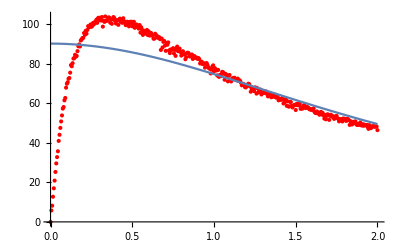

```mathematica
Show[ListPlot[v1000,PlotStyle->Red],Plot[(a (x/b-r))/(1+(x/b)^2)/.{a->-0.3771708405534093,b->2.2144891723410827,r->239.31692055890608},{x,0,2}]]
```

## Manipulate

```mathematica
Manipulate[Show[Plot[(a (x/b-r))/(1+(x/b)^2),{x,0,2},PlotRange->All],ListPlot[v1000]],{a,0,500},{b,000.1,2},{r,-10,10}]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v1200=blist[[3;;All,{14,11}]] 
FindFit[v1200,a*(x/b-r)/(1+(x/b)^2),{a,b,r},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,6.1},{0.01,8.4},{0.015,12.6},{0.02,17.25},{0.025,21},{0.03,25.1},{0.035,29.15},{0.04,33.35},{0.045,37.7},{0.05,41.7},{0.055,44.85},{0.06,47.9},{0.065,51.7},{0.07,54.8},{0.075,57.85},{0.08,60.35},{0.085,64.35},{0.09,66.15},{0.095,70.2},{0.1,71.55},{0.105,73.45},{0.11,75.55},{0.115,77.95},{0.12,79.95},{0.125,81.7},{0.13,82.95},{0.135,86},{0.14,87.95},{0.145,88.85},{0.15,91.3},{0.155,92.5},{0.16,93.4},{0.165,92.3},{0.17,92.95},{0.175,96.65},{0.18,98.35},{0.185,98.4},{0.19,99.5},{0.195,100.75},{0.2,100.55},{0.205,102.95},{0.21,102.15},{0.215,102.65},{0.22,102.2},{0.225,105.35},{0.23,103.45},{0.235,105.75},{0.24,107.85},{0.245,106.85},{0.25,107.65},{0.255,110.2},{0.26,108.25},{0.265,105.5},{0.27,108.65},{0.275,111.25},{0.28,107.55},{0.285,110.25},{0.29,112.3},{0.295,112.9},{0.3,111.1},{0.305,112.2},{0.31,113.2},{0.315,113.6},{0.32,113.2},{0.325,109.85},{0.33,114.75},{0.335,115.45},{0.34,110},{0.345,113.3},{0.35,113.35},{0.355,113.7},{0.36,114.7},{0.365,115.7},{0.37,110.6},{0.375,115.1},{0.38,116.35},{0.385,114.95},{0.39,115.95},{0.395,112.8},{0.4,114.65},{0.405,116.4},{0.41,112.85},{0.415,115.3},{0.42,116.8},{0.425,111.25},{0.43,114.75},{0.435,114.95},{0.44,114.2},{0.445,111.85},{0.45,112.7},{0.455,114.25},{0.46,113.3},{0.465,109.6},{0.47,114.85},{0.475,114.55},{0.48,115.3},{0.485,113.25},{0.49,115.1},{0.495,114.9},{0.5,111.15},{0.505,113.05},{0.51,114.1},{0.515,110.1},{0.52,115.15},{0.525,114.55},{0.53,112.6},{0.535,112.95},{0.54,112.1},{0.545,112.1},{0.55,112.1},{0.555,111.35},{0.56,111.7},{0.565,111.2},{0.57,110.85},{0.575,111.9},{0.58,111.1},{0.585,113},{0.59,113.05},{0.595,112.35},{0.6,111.45},{0.605,111.95},{0.61,112.4},{0.615,111.15},{0.62,109},{0.625,111.1},{0.63,110.1},{0.635,109.6},{0.64,107.85},{0.645,107.75},{0.65,107.7},{0.655,107.95},{0.66,107.6},{0.665,109.3},{0.67,103.9},{0.675,104.7},{0.68,106.05},{0.685,106.7},{0.69,106.75},{0.695,107.15},{0.7,105.55},{0.705,105.05},{0.71,106.65},{0.715,105.8},{0.72,103.9},{0.725,105.4},{0.73,104.65},{0.735,104.65},{0.74,104.75},{0.745,100.4},{0.75,100.35},{0.755,103.8},{0.76,105.5},{0.765,104.85},{0.77,102.5},{0.775,102.35},{0.78,103},{0.785,102.75},{0.79,103.6},{0.795,102.6},{0.8,102.2},{0.805,102.25},{0.81,101.65},{0.815,102.8},{0.82,101.6},{0.825,101.05},{0.83,99.8},{0.835,101.3},{0.84,100.45},{0.845,100.7},{0.85,101.65},{0.855,98.65},{0.86,100.3},{0.865,98.5},{0.87,99},{0.875,99.05},{0.88,96.9},{0.885,94.9},{0.89,97.9},{0.895,98.3},{0.9,98.6},{0.905,98},{0.91,98},{0.915,94.8},{0.92,97.05},{0.925,96.6},{0.93,95.25},{0.935,97.4},{0.94,95.4},{0.945,96.25},{0.95,95.45},{0.955,95.2},{0.96,94.75},{0.965,94.3},{0.97,94.5},{0.975,94.6},{0.98,95.05},{0.985,94.6},{0.99,93.4},{0.995,93.7},{1,93.1},{1.005,94.75},{1.01,93.3},{1.015,91.85},{1.02,92.8},{1.025,92.35},{1.03,92.3},{1.035,91.8},{1.04,92.05},{1.045,91.15},{1.05,91},{1.055,87.3},{1.06,91.05},{1.065,90},{1.07,90.6},{1.075,91.15},{1.08,91.1},{1.085,86.2},{1.09,89.75},{1.095,89.6},{1.1,89.25},{1.105,88.85},{1.11,90.15},{1.115,89.05},{1.12,87.25},{1.125,87.6},{1.13,86.95},{1.135,88.8},{1.14,88.4},{1.145,88.1},{1.15,88.25},{1.155,88.45},{1.16,87.6},{1.165,83.65},{1.17,83.1},{1.175,85.25},{1.18,86.65},{1.185,86.8},{1.19,82.85},{1.195,83.95},{1.2,85.3},{1.205,85.65},{1.21,84.7},{1.215,85.45},{1.22,83.3},{1.225,84.8},{1.23,84.3},{1.235,83.5},{1.24,84},{1.245,84.1},{1.25,84.7},{1.255,83.15},{1.26,82.15},{1.265,83.25},{1.27,82.05},{1.275,82.6},{1.28,78.75},{1.285,79.9},{1.29,81.8},{1.295,83.15},{1.3,81.85},{1.305,79.75},{1.31,78.3},{1.315,81.1},{1.32,79.9},{1.325,78.75},{1.33,80.65},{1.335,79.2},{1.34,79.45},{1.345,78.65},{1.35,79.5},{1.355,79.45},{1.36,79.2},{1.365,78.6},{1.37,76.8},{1.375,74.9},{1.38,78.25},{1.385,74.7},{1.39,77.1},{1.395,78.4},{1.4,78.7},{1.405,77.2},{1.41,77.35},{1.415,77.25},{1.42,75.5},{1.425,75.2},{1.43,77.3},{1.435,74.35},{1.44,75},{1.445,74.95},{1.45,73.1},{1.455,75.55},{1.46,74.55},{1.465,75.45},{1.47,75.45},{1.475,74.75},{1.48,74.75},{1.485,74.85},{1.49,74.3},{1.495,74.35},{1.5,73},{1.505,72.6},{1.51,73.6},{1.515,74.35},{1.52,73.9},{1.525,73.7},{1.53,72.7},{1.535,72.7},{1.54,73.45},{1.545,73.25},{1.55,73.45},{1.555,71.1},{1.56,72.7},{1.565,71.85},{1.57,72.85},{1.575,72.35},{1.58,71.6},{1.585,71.8},{1.59,72.05},{1.595,69.5},{1.6,69.95},{1.605,71.2},{1.61,70.5},{1.615,69.75},{1.62,69.6},{1.625,67.55},{1.63,68.35},{1.635,69.2},{1.64,68.7},{1.645,68.75},{1.65,68.95},{1.655,69.95},{1.66,66.45},{1.665,68.35},{1.67,67.9},{1.675,68.5},{1.68,68.15},{1.685,69.35},{1.69,69.3},{1.695,67.45},{1.7,67.6},{1.705,67.2},{1.71,66.3},{1.715,66.85},{1.72,68.15},{1.725,66.95},{1.73,66.4},{1.735,66.3},{1.74,66.65},{1.745,66.55},{1.75,67.35},{1.755,66.4},{1.76,66.15},{1.765,65},{1.77,65.45},{1.775,65.5},{1.78,65},{1.785,66.3},{1.79,64.55},{1.795,64.7},{1.8,65.65},{1.805,64.45},{1.81,62.5},{1.815,63.8},{1.82,63.4},{1.825,64.15},{1.83,63.2},{1.835,63.55},{1.84,64.55},{1.845,64.75},{1.85,63.55},{1.855,63.15},{1.86,64.55},{1.865,63.9},{1.87,62.7},{1.875,63.05},{1.88,61.55},{1.885,62.95},{1.89,60.25},{1.895,61.35},{1.9,62.75},{1.905,61.25},{1.91,62.55},{1.915,60.95},{1.92,62.15},{1.925,61.75},{1.93,61.55},{1.935,60.3},{1.94,59.75},{1.945,59.4},{1.95,58.45},{1.955,60.8},{1.96,61.1},{1.965,60.8},{1.97,61.6},{1.975,61.15},{1.98,60.8},{1.985,60.45},{1.99,59.75},{1.995,60.3},{2,60}}

{a→-209.853,b→-0.546647,r→0.126624}

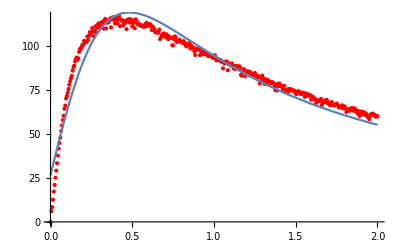

```mathematica
Show[ListPlot[v1200,PlotStyle->Red],Plot[(a (x/b-r))/(1+(x/b)^2)/.{a->-209.85319441674324,b->-0.5466470133616779,r->0.12662352548720746},{x,0,2}]]
```

## Manipulate

```mathematica
Manipulate[Show[Plot[(a (x/b-r))/(1+(x/b)^2),{x,0,2},PlotRange->All],ListPlot[v1200]],{a,0,500},{b,000.1,2},{r,-10,10}]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v1400=blist[[3;;All,{14,12}]] 
FindFit[v1400,a*(x/b-r)/(1+(x/b)^2),{a,b,r},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,5.85},{0.01,8.25},{0.015,12.4},{0.02,16.65},{0.025,20.9},{0.03,24.75},{0.035,30},{0.04,33.65},{0.045,37.6},{0.05,41.2},{0.055,44.3},{0.06,49},{0.065,52.8},{0.07,55.05},{0.075,58.7},{0.08,62.4},{0.085,65.2},{0.09,69.1},{0.095,71.25},{0.1,73.55},{0.105,73.75},{0.11,78.1},{0.115,78.25},{0.12,80.05},{0.125,84.55},{0.13,87.3},{0.135,89.65},{0.14,90.4},{0.145,91.6},{0.15,93.85},{0.155,95.35},{0.16,96.8},{0.165,98.05},{0.17,100.8},{0.175,99.7},{0.18,103.3},{0.185,103.75},{0.19,104.4},{0.195,107.6},{0.2,108.7},{0.205,107},{0.21,108.75},{0.215,111.45},{0.22,111.25},{0.225,114.15},{0.23,114.05},{0.235,115.55},{0.24,115.45},{0.245,115.95},{0.25,117.9},{0.255,116.85},{0.26,118.75},{0.265,114.95},{0.27,121.25},{0.275,122.2},{0.28,119.8},{0.285,121.45},{0.29,123},{0.295,121.5},{0.3,120.65},{0.305,123.6},{0.31,125.65},{0.315,123.3},{0.32,125.4},{0.325,124},{0.33,122.7},{0.335,121.75},{0.34,126.25},{0.345,127.75},{0.35,123.45},{0.355,126.7},{0.36,125.65},{0.365,129.15},{0.37,125.25},{0.375,128.15},{0.38,126.65},{0.385,128.15},{0.39,128.65},{0.395,125.4},{0.4,124.05},{0.405,130.55},{0.41,128.95},{0.415,130.55},{0.42,128.85},{0.425,130.75},{0.43,131.15},{0.435,124.75},{0.44,129.55},{0.445,130.05},{0.45,130.4},{0.455,132.55},{0.46,132.3},{0.465,130.5},{0.47,131.1},{0.475,130.6},{0.48,129.35},{0.485,132.75},{0.49,132.05},{0.495,130.2},{0.5,129.95},{0.505,125.2},{0.51,130.45},{0.515,131.8},{0.52,131.9},{0.525,130.3},{0.53,129.45},{0.535,129.05},{0.54,131.35},{0.545,130.5},{0.55,128.65},{0.555,129.55},{0.56,129.55},{0.565,128.4},{0.57,127.75},{0.575,130.7},{0.58,131.6},{0.585,126.05},{0.59,128.9},{0.595,130.65},{0.6,128.8},{0.605,129.25},{0.61,128.8},{0.615,129.4},{0.62,130.35},{0.625,129.25},{0.63,125.55},{0.635,129.25},{0.64,128},{0.645,126.05},{0.65,126.2},{0.655,125.7},{0.66,129},{0.665,127.9},{0.67,126.8},{0.675,126.1},{0.68,125.5},{0.685,127.45},{0.69,126.15},{0.695,126.65},{0.7,125.8},{0.705,121.7},{0.71,121.6},{0.715,125.45},{0.72,125.35},{0.725,125.55},{0.73,125.8},{0.735,126.65},{0.74,124.65},{0.745,122.9},{0.75,121.3},{0.755,123},{0.76,123.95},{0.765,123.45},{0.77,124.5},{0.775,124.25},{0.78,124.55},{0.785,125},{0.79,121.05},{0.795,121.05},{0.8,119.85},{0.805,121.25},{0.81,120.65},{0.815,115.6},{0.82,121},{0.825,120.05},{0.83,122.35},{0.835,121.3},{0.84,121.7},{0.845,116.2},{0.85,119.45},{0.855,120.3},{0.86,120.15},{0.865,120.25},{0.87,119.85},{0.875,119.65},{0.88,117.9},{0.885,119.35},{0.89,118.45},{0.895,113.8},{0.9,117.05},{0.905,118.9},{0.91,120},{0.915,117.25},{0.92,114},{0.925,116.6},{0.93,115.9},{0.935,114.45},{0.94,116.6},{0.945,117.55},{0.95,117.55},{0.955,117.65},{0.96,115.95},{0.965,116.3},{0.97,115.75},{0.975,117.05},{0.98,116.2},{0.985,114.95},{0.99,111.05},{0.995,113.85},{1,113.85},{1.005,110.95},{1.01,113.75},{1.015,113.7},{1.02,109.8},{1.025,111.2},{1.03,113.95},{1.035,109.4},{1.04,113.8},{1.045,112.7},{1.05,114.35},{1.055,112.6},{1.06,108.8},{1.065,108.5},{1.07,108.05},{1.075,110.3},{1.08,109.65},{1.085,111.05},{1.09,109.45},{1.095,110.25},{1.1,110.25},{1.105,110.85},{1.11,110.3},{1.115,108.85},{1.12,109.2},{1.125,108.75},{1.13,105.8},{1.135,107.7},{1.14,108.75},{1.145,109.6},{1.15,108.7},{1.155,106.8},{1.16,104.15},{1.165,108.85},{1.17,107.8},{1.175,106},{1.18,101},{1.185,106.55},{1.19,102.5},{1.195,104.65},{1.2,107.15},{1.205,105.55},{1.21,104.6},{1.215,103.95},{1.22,104.8},{1.225,105.4},{1.23,104.65},{1.235,106},{1.24,101.6},{1.245,103.95},{1.25,104.7},{1.255,102.4},{1.26,101.1},{1.265,102.2},{1.27,101.95},{1.275,101.65},{1.28,102.9},{1.285,100.65},{1.29,102.5},{1.295,102.2},{1.3,101.45},{1.305,99.4},{1.31,97.8},{1.315,97.15},{1.32,100.4},{1.325,99.45},{1.33,97.4},{1.335,100.45},{1.34,100.65},{1.345,98.95},{1.35,100.1},{1.355,99},{1.36,99.1},{1.365,98.65},{1.37,98.35},{1.375,98.2},{1.38,98.95},{1.385,99.2},{1.39,96.15},{1.395,99.35},{1.4,93.95},{1.405,94},{1.41,98.1},{1.415,97.75},{1.42,96.55},{1.425,95.35},{1.43,95.9},{1.435,98.2},{1.44,95.6},{1.445,96.75},{1.45,97.05},{1.455,97.45},{1.46,94.7},{1.465,92.9},{1.47,94.9},{1.475,94.35},{1.48,95.2},{1.485,94.95},{1.49,94.25},{1.495,93.05},{1.5,92.1},{1.505,92.7},{1.51,94.5},{1.515,93.1},{1.52,93.15},{1.525,93.2},{1.53,92.15},{1.535,93.15},{1.54,91.9},{1.545,88.3},{1.55,90.65},{1.555,91.45},{1.56,88.6},{1.565,88.9},{1.57,90.55},{1.575,90.05},{1.58,89.25},{1.585,89.55},{1.59,87.3},{1.595,86.45},{1.6,89.35},{1.605,91},{1.61,90.65},{1.615,89.25},{1.62,90.05},{1.625,88.85},{1.63,89.3},{1.635,88.8},{1.64,88.65},{1.645,89.25},{1.65,88},{1.655,87.1},{1.66,88.5},{1.665,88.5},{1.67,86.1},{1.675,87.5},{1.68,87.25},{1.685,87.4},{1.69,87.9},{1.695,87.1},{1.7,83.3},{1.705,86.2},{1.71,84.85},{1.715,86.25},{1.72,85.25},{1.725,84.35},{1.73,85.25},{1.735,86.5},{1.74,81.9},{1.745,83.35},{1.75,84.25},{1.755,85.3},{1.76,84.8},{1.765,83.2},{1.77,84.1},{1.775,84.65},{1.78,83.35},{1.785,83.15},{1.79,83.7},{1.795,83.35},{1.8,82.75},{1.805,82.55},{1.81,83.35},{1.815,80.6},{1.82,81.65},{1.825,82.05},{1.83,82.35},{1.835,80.5},{1.84,81.75},{1.845,82.1},{1.85,82.2},{1.855,80.9},{1.86,82.55},{1.865,81.5},{1.87,81.95},{1.875,80.55},{1.88,81.75},{1.885,79},{1.89,79.7},{1.895,81.1},{1.9,81.4},{1.905,77.15},{1.91,78.9},{1.915,76.75},{1.92,79.65},{1.925,79.45},{1.93,76.6},{1.935,78.75},{1.94,78.55},{1.945,79.1},{1.95,79.2},{1.955,77.8},{1.96,75.15},{1.965,78.05},{1.97,77.7},{1.975,77.8},{1.98,77.05},{1.985,76.1},{1.99,77.95},{1.995,78.35},{2,78.6}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→-0.539594,b→3.4655,r→210.467}

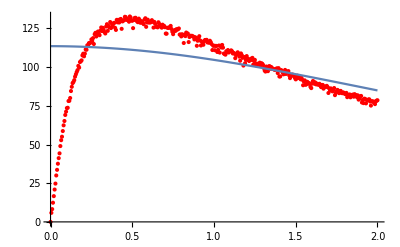

```mathematica
Show[ListPlot[v1400,PlotStyle->Red],Plot[(a (x/b-r))/(1+(x/b)^2)/.{a->-0.5395936315199845,b->3.465496064258223,r->210.46704552842854},{x,0,2}]]
```

## Manipulate

```mathematica
Manipulate[Show[Plot[(a (x/b-r))/(1+(x/b)^2),{x,0,2},PlotRange->All],ListPlot[v1400]],{a,0,500},{b,000.1,2},{r,-10,10}]
```

```mathematica
blist=Import["\\\\files.brown.edu\\Home\\nlawandy\\Desktop\\Copy of Ruby crystal, f-25mm with 580nm filter, EIIC.csv"]
v1600=blist[[3;;All,{14,13}]] 
FindFit[v1600,a*(x/b-r)/(1+(x/b)^2),{a,b,r},x]
```

{{,,19-05-02 20-1-26 Ruby turned with 580nm filter 25mW,19-05-02 20-43-4 Ruby turned with 580nm filter 50mW,19-05-02 21-24-32 Ruby turned with 580nm filter 100mW,19-05-02 22-6-6 Ruby turned with 580nm filter 200mW,19-05-02 22-47-40 Ruby turned with 580nm filter 400mW,19-05-02 23-29-15 Ruby turned with 580nm filter 600mW,19-05-03 0-10-48 Ruby turned with 580nm filter 800mW,19-05-03 0-52-4 Ruby turned with 580nm filter 1000mW,19-05-03 1-33-35 Ruby turned with 580nm filter 1200mW,19-05-03 2-15-21 Ruby turned with 580nm filter 1400mW,19-05-03 2-57-10 Ruby turned with 580nm filter 1600mW,,,,,,,,,,,,,,,,,,},401,{399,4,0.05,0.202,0.77,2.85,9.43,19.13,28.6,46.45,60,78.6,95.95,2,,,,,,,,,,,,,,,,,}}
 |  |  |  |

{{0,0},{0.005,6.1},{0.01,8.4},{0.015,12.35},{0.02,16.05},{0.025,20.95},{0.03,25.1},{0.035,29.35},{0.04,33.2},{0.045,37.05},{0.05,39.25},{0.055,44.9},{0.06,48.9},{0.065,52.15},{0.07,55.95},{0.075,57.6},{0.08,61.8},{0.085,65.65},{0.09,67.35},{0.095,71.35},{0.1,72.35},{0.105,74.6},{0.11,79.2},{0.115,79.4},{0.12,83.1},{0.125,86},{0.13,89.25},{0.135,91.5},{0.14,91.45},{0.145,95.15},{0.15,96.3},{0.155,98.9},{0.16,97.25},{0.165,99.1},{0.17,102.85},{0.175,104.7},{0.18,106.75},{0.185,109.1},{0.19,111.4},{0.195,112.45},{0.2,112.95},{0.205,112.8},{0.21,113.75},{0.215,112.5},{0.22,116.7},{0.225,118.25},{0.23,120.4},{0.235,120.5},{0.24,121.8},{0.245,120},{0.25,124.3},{0.255,123.95},{0.26,122.2},{0.265,124.75},{0.27,127.6},{0.275,127.3},{0.28,125.55},{0.285,128.7},{0.29,130.45},{0.295,131.4},{0.3,130.9},{0.305,131},{0.31,133.3},{0.315,134.2},{0.32,132.35},{0.325,133.55},{0.33,133.3},{0.335,135.65},{0.34,131.9},{0.345,134.85},{0.35,138.05},{0.355,137.5},{0.36,137.45},{0.365,137.1},{0.37,137.3},{0.375,140.3},{0.38,138.7},{0.385,140},{0.39,134.35},{0.395,133.65},{0.4,137.85},{0.405,135.45},{0.41,137.1},{0.415,142.4},{0.42,137.25},{0.425,140.05},{0.43,138.05},{0.435,141.05},{0.44,140.8},{0.445,142.9},{0.45,143.1},{0.455,145.05},{0.46,141.05},{0.465,141.85},{0.47,143},{0.475,144.8},{0.48,145.7},{0.485,142.85},{0.49,144.25},{0.495,146.35},{0.5,145.6},{0.505,147.05},{0.51,144.45},{0.515,144.3},{0.52,138.6},{0.525,142.55},{0.53,143.1},{0.535,139.4},{0.54,144.6},{0.545,144.6},{0.55,141.85},{0.555,143.95},{0.56,146.4},{0.565,145.95},{0.57,144.3},{0.575,140.2},{0.58,144.1},{0.585,144.25},{0.59,142.25},{0.595,146.15},{0.6,141.2},{0.605,139.65},{0.61,144.1},{0.615,145.4},{0.62,145.45},{0.625,144},{0.63,144.7},{0.635,147.15},{0.64,144.9},{0.645,141.35},{0.65,143.2},{0.655,143.4},{0.66,143.9},{0.665,143.6},{0.67,145.95},{0.675,144.8},{0.68,141.4},{0.685,138.75},{0.69,142.85},{0.695,145.25},{0.7,145.05},{0.705,144.45},{0.71,142.75},{0.715,143},{0.72,142.35},{0.725,142.25},{0.73,134.85},{0.735,140.25},{0.74,143.9},{0.745,144.4},{0.75,140.05},{0.755,143.55},{0.76,143},{0.765,140.1},{0.77,141.4},{0.775,141.45},{0.78,139.5},{0.785,141.9},{0.79,137.25},{0.795,135.85},{0.8,142.15},{0.805,138.4},{0.81,142.2},{0.815,141.05},{0.82,141.45},{0.825,140.8},{0.83,139.35},{0.835,135.65},{0.84,136.1},{0.845,139.05},{0.85,138.4},{0.855,140.45},{0.86,140},{0.865,138.65},{0.87,139.5},{0.875,138.9},{0.88,137.9},{0.885,137.9},{0.89,136.5},{0.895,137.6},{0.9,137.25},{0.905,139.6},{0.91,137.95},{0.915,137.45},{0.92,137.25},{0.925,136.2},{0.93,135.65},{0.935,136.55},{0.94,134.1},{0.945,137},{0.95,136.2},{0.955,138.45},{0.96,130.1},{0.965,134.75},{0.97,134.95},{0.975,133.8},{0.98,133.65},{0.985,134.7},{0.99,134.1},{0.995,136.3},{1,135.65},{1.005,133},{1.01,129.85},{1.015,131.55},{1.02,128.4},{1.025,127.7},{1.03,134.7},{1.035,136.5},{1.04,131.15},{1.045,131},{1.05,127.35},{1.055,131.4},{1.06,129.4},{1.065,130.95},{1.07,131},{1.075,132.9},{1.08,130.65},{1.085,132.55},{1.09,132.65},{1.095,132.5},{1.1,132.7},{1.105,131.55},{1.11,131.75},{1.115,130.05},{1.12,130.9},{1.125,131.2},{1.13,129.05},{1.135,130.6},{1.14,129.8},{1.145,128.35},{1.15,123.15},{1.155,127},{1.16,127.75},{1.165,126.05},{1.17,128.4},{1.175,129.4},{1.18,127.7},{1.185,126},{1.19,128.2},{1.195,128},{1.2,125.85},{1.205,127.1},{1.21,127.7},{1.215,127.1},{1.22,123.55},{1.225,126.1},{1.23,126.25},{1.235,123.45},{1.24,124.1},{1.245,122},{1.25,123.8},{1.255,125},{1.26,124.3},{1.265,124.75},{1.27,125.55},{1.275,125.8},{1.28,123.45},{1.285,122.9},{1.29,118.5},{1.295,120.3},{1.3,121.25},{1.305,116.6},{1.31,123.15},{1.315,122.65},{1.32,120.9},{1.325,121.85},{1.33,122.05},{1.335,115.5},{1.34,118.45},{1.345,120.55},{1.35,118.7},{1.355,120.45},{1.36,121.5},{1.365,117.85},{1.37,116.2},{1.375,116.45},{1.38,119.35},{1.385,118.25},{1.39,119.15},{1.395,119.5},{1.4,117.15},{1.405,118.25},{1.41,114.5},{1.415,119.25},{1.42,118.9},{1.425,117.9},{1.43,119.05},{1.435,117.5},{1.44,115.9},{1.445,116.75},{1.45,118.05},{1.455,118.25},{1.46,112.9},{1.465,114.9},{1.47,115.95},{1.475,116.55},{1.48,115.2},{1.485,114.3},{1.49,113.9},{1.495,114.75},{1.5,109.6},{1.505,111.55},{1.51,114.65},{1.515,113.45},{1.52,115.25},{1.525,115.25},{1.53,113.3},{1.535,113.3},{1.54,111.35},{1.545,113.5},{1.55,108.6},{1.555,112.1},{1.56,113.05},{1.565,112.45},{1.57,113.65},{1.575,112.3},{1.58,111.6},{1.585,110.85},{1.59,110.5},{1.595,109.95},{1.6,109.1},{1.605,107.6},{1.61,108.85},{1.615,112.05},{1.62,110.7},{1.625,105.6},{1.63,106.9},{1.635,110.35},{1.64,108.95},{1.645,107.45},{1.65,110.1},{1.655,109.35},{1.66,109.05},{1.665,108.35},{1.67,108.5},{1.675,105.8},{1.68,106.3},{1.685,109.8},{1.69,105.1},{1.695,106.5},{1.7,107.05},{1.705,107.05},{1.71,106.1},{1.715,107.5},{1.72,104.95},{1.725,106.85},{1.73,107},{1.735,106.45},{1.74,104.65},{1.745,104.35},{1.75,101.85},{1.755,105.55},{1.76,105},{1.765,104.5},{1.77,104.45},{1.775,104.85},{1.78,104.1},{1.785,104.75},{1.79,105.45},{1.795,103},{1.8,102.1},{1.805,104.05},{1.81,101.85},{1.815,99.65},{1.82,100.45},{1.825,99.9},{1.83,102.75},{1.835,101.7},{1.84,102.75},{1.845,103.25},{1.85,101.4},{1.855,102.4},{1.86,102.7},{1.865,100},{1.87,99.35},{1.875,101},{1.88,101.2},{1.885,102.25},{1.89,100.8},{1.895,100.2},{1.9,97.1},{1.905,98.4},{1.91,96},{1.915,99.55},{1.92,98.6},{1.925,98.75},{1.93,94.9},{1.935,97.75},{1.94,95.55},{1.945,97.1},{1.95,97},{1.955,98.1},{1.96,96.8},{1.965,96.1},{1.97,96.7},{1.975,96.55},{1.98,96.25},{1.985,97.4},{1.99,97.7},{1.995,96},{2,95.95}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→-0.817659,b→5.25135,r→152.305}

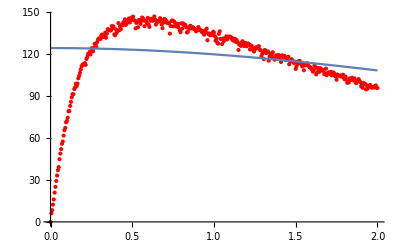

```mathematica
Show[ListPlot[v1600,PlotStyle->Red],Plot[(a (x/b-r))/(1+(x/b)^2)/.{a->-0.8176593386637848,b->5.251353826758949,r->152.30486841053158},{x,0,2}]]
```

## Manipulate

```mathematica
Manipulate[Show[Plot[(a (x/b-r))/(1+(x/b)^2),{x,0,2},PlotRange->All],ListPlot[v1600]],{a,0,500},{b,000.1,2},{r,-10,10}]
```